## Section 3: formulation

definition of real spherical harmonic. eq. (3.7)

```mathematica
realkl[k_,l_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,θ,φ]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,θ,0],l==0},{(√2)*ComplexExpand[Im[SphericalHarmonicY[k,l,θ,φ]]]//FullSimplify,l<0}}]
```

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0},{(√2)*ComplexExpand[Im[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l<0}}]
```

```mathematica
Clear[η,t,ϕ,ϕ1,ϕ2,ϕ3, η1, η2, η3]
```

```mathematica
ϕ[r_,θ_,φ_,t_]:=e*ϕ1[r,θ,φ,t]+e^2*ϕ2[r,θ,φ,t]+e^3*ϕ3[r,θ,φ,t];
η[θ_,φ_,t_]:=e* η1[θ,φ,t]+e^2* η2[θ,φ,t]+e^3* η3[θ,φ,t];
```

```mathematica
ϕ[a_,b_,c_,d_]:=e*ϕ1[a,b,c,d]+e^2*ϕ2[a,b,c,d]+e^3*ϕ3[a,b,c,d];
η[a_,b_,c_]:=e* η1[a,b,c]+e^2* η2[a,b,c]+e^3* η3[a,b,c];
```

```mathematica
Series[(Derivative[1,0,0,0][phi][r,θ,φ,t])^2/.r->1+e*η[θ,φ,t],{e,0,1}]
```

(phi^(1,0,0,0)[1,θ,φ,t])^2+2 η[θ,φ,t] phi^(1,0,0,0)[1,θ,φ,t] phi^(2,0,0,0)[1,θ,φ,t] e+O[e]^2

```mathematica
kinematicst=η[θ,φ,t]+{1/r*D[ϕ[r,θ,φ,t],θ],1/(r*Sin[θ])*D[ϕ[r,θ,φ,t],φ]}.{1/r*D[η[θ,φ,t],θ],1/(r*Sin[θ])*D[η[θ,φ,t],φ]}-D[ϕ[r,θ,φ,t],r](*/.r->1+e*η[θ,φ,t]*)
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+1/r^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ1^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ2^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ3^(0,0,1,0)[r,θ,φ,t])+1/r^2(e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ1^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ2^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ3^(0,1,0,0)[r,θ,φ,t])-e ϕ1^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ2^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ3^(1,0,0,0)[r,θ,φ,t]

```mathematica
kinematicst=η[θ,φ,t]+Grad[ϕ[r,θ,φ,t],{r,θ,φ},"Spherical"].Grad[η[θ,φ,t],{r,θ,φ},"Spherical"]-D[ϕ[r,θ,φ,t],r]/.r->1+η[θ,φ,t]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+(Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ1^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^2 ϕ2^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^3 ϕ3^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]))/(1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t])^2+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ1^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^2 ϕ2^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^3 ϕ3^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]))/(1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t])^2-e ϕ1^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]-e^2 ϕ2^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]-e^3 ϕ3^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]

```mathematica
kinematicstpertr1=Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ1^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ1^(0,1,0,0)[1,θ,φ,t]-ϕ2^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ1^(0,1,0,0)[1,θ,φ,t]-ϕ3^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ2^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ1^(3,0,0,0)[1,θ,φ,t])

```mathematica
kinematicst=(Csc[θ]^2 (e Derivative[0,1,0][η1][θ,φ,t]+e^2 Derivative[0,1,0][η2][θ,φ,t]+e^3 Derivative[0,1,0][η3][θ,φ,t]) (e Derivative[0,0,1,0][ϕ1][r,θ,φ,t]+e^2 Derivative[0,0,1,0][ϕ2][r,θ,φ,t]+e^3 Derivative[0,0,1,0][ϕ3][r,θ,φ,t]))/r^2+((e Derivative[1,0,0][η1][θ,φ,t]+e^2 Derivative[1,0,0][η2][θ,φ,t]+e^3 Derivative[1,0,0][η3][θ,φ,t]) (e Derivative[0,1,0,0][ϕ1][r,θ,φ,t]+e^2 Derivative[0,1,0,0][ϕ2][r,θ,φ,t]+e^3 Derivative[0,1,0,0][ϕ3][r,θ,φ,t]))/r^2;
```

```mathematica
(Norm[Grad[ϕ[r,θ,φ,t],{r,θ,φ},"Spherical"]])^2
```

Abs[(Csc[θ] ϕ^(0,0,1,0)[r,θ,φ,t])/r]^2+Abs[(ϕ^(0,1,0,0)[r,θ,φ,t])/r]^2+Abs[ϕ^(1,0,0,0)[r,θ,φ,t]]^2

```mathematica
curvature=2/r+(-Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t]-Cot[θ] Derivative[1,0,0][η][θ,φ,t]-Derivative[2,0,0][η][θ,φ,t])/r^2+1/r^4(Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t] (Derivative[1,0,0][η][θ,φ,t])^2+Cot[θ] (Derivative[1,0,0][η][θ,φ,t])^3+2 Csc[θ]^2 Derivative[0,1,0][η][θ,φ,t] Derivative[1,0,0][η][θ,φ,t] Derivative[1,1,0][η][θ,φ,t]+3 (Derivative[1,0,0][η][θ,φ,t])^2 Derivative[2,0,0][η][θ,φ,t]);
```

```mathematica
normalst=D[ϕ[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ[r,θ,φ,t],φ]^2)/r^2+D[ϕ[r,θ,φ,t],θ]^2/r^2+D[ϕ[r,θ,φ,t],r]^2)(*+2*δ*D[ϕ[r,θ,φ,t],r,r]*)-1/We*(curvature)(*e*(1+η[θ,φ,t])*Cos[θ]*Sin[t]*)
```

-1/We(2/r+1/r^2(-Csc[θ]^2 (e η1^(0,2,0)[θ,φ,t]+e^2 η2^(0,2,0)[θ,φ,t]+e^3 η3^(0,2,0)[θ,φ,t])-Cot[θ] (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])-e η1^(2,0,0)[θ,φ,t]-e^2 η2^(2,0,0)[θ,φ,t]-e^3 η3^(2,0,0)[θ,φ,t])+1/r^4(Csc[θ]^2 (e η1^(0,2,0)[θ,φ,t]+e^2 η2^(0,2,0)[θ,φ,t]+e^3 η3^(0,2,0)[θ,φ,t]) (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2+Cot[θ] (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^3+2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e η1^(1,1,0)[θ,φ,t]+e^2 η2^(1,1,0)[θ,φ,t]+e^3 η3^(1,1,0)[θ,φ,t])+3 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2 (e η1^(2,0,0)[θ,φ,t]+e^2 η2^(2,0,0)[θ,φ,t]+e^3 η3^(2,0,0)[θ,φ,t])))+e ϕ1^(0,0,0,1)[r,θ,φ,t]+e^2 ϕ2^(0,0,0,1)[r,θ,φ,t]+e^3 ϕ3^(0,0,0,1)[r,θ,φ,t]+1/2 ((Csc[θ]^2 (e ϕ1^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ2^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ3^(0,0,1,0)[r,θ,φ,t])^2)/r^2+((e ϕ1^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ2^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ3^(0,1,0,0)[r,θ,φ,t])^2)/r^2+(e ϕ1^(1,0,0,0)[r,θ,φ,t]+e^2 ϕ2^(1,0,0,0)[r,θ,φ,t]+e^3 ϕ3^(1,0,0,0)[r,θ,φ,t])^2)

```mathematica
normalst=-1/We(2/r+(-Csc[θ]^2 Derivative[0,2][η][θ,φ]-Cot[θ] Derivative[1,0][η][θ,φ]-Derivative[2,0][η][θ,φ])/r^2+1/(2 r^4)(3 Csc[θ]^4 (Derivative[0,1][η][θ,φ])^2 Derivative[0,2][η][θ,φ]-Cot[θ] Csc[θ]^2 (Derivative[0,1][η][θ,φ])^2 Derivative[1,0][η][θ,φ]+Csc[θ]^2 Derivative[0,2][η][θ,φ] (Derivative[1,0][η][θ,φ])^2+Cot[θ] (Derivative[1,0][η][θ,φ])^3+4 Csc[θ]^2 Derivative[0,1][η][θ,φ] Derivative[1,0][η][θ,φ] Derivative[1,1][η][θ,φ]+Csc[θ]^2 (Derivative[0,1][η][θ,φ])^2 Derivative[2,0][η][θ,φ]+3 (Derivative[1,0][η][θ,φ])^2 Derivative[2,0][η][θ,φ]))+e Derivative[0,0,0,1][ϕ1][r,θ,φ,t]+e^2 Derivative[0,0,0,1][ϕ2][r,θ,φ,t]+e^3 Derivative[0,0,0,1][ϕ3][r,θ,φ,t]+1/2 ((Csc[θ]^2 (e Derivative[0,0,1,0][ϕ1][r,θ,φ,t]+e^2 Derivative[0,0,1,0][ϕ2][r,θ,φ,t]+e^3 Derivative[0,0,1,0][ϕ3][r,θ,φ,t])^2)/r^2+((e Derivative[0,1,0,0][ϕ1][r,θ,φ,t]+e^2 Derivative[0,1,0,0][ϕ2][r,θ,φ,t]+e^3 Derivative[0,1,0,0][ϕ3][r,θ,φ,t])^2)/r^2+(e Derivative[1,0,0,0][ϕ1][r,θ,φ,t]+e^2 Derivative[1,0,0,0][ϕ2][r,θ,φ,t]+e^3 Derivative[1,0,0,0][ϕ3][r,θ,φ,t])^2);
```

```mathematica
kinematicstpertr1=Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ1^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ1^(0,1,0,0)[1,θ,φ,t]-ϕ2^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ1^(0,1,0,0)[1,θ,φ,t]-ϕ3^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ2^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ1^(3,0,0,0)[1,θ,φ,t])

```mathematica
Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ1^(0,1,0,0)[1,θ,φ,t]-ϕ3^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ2^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ1^(3,0,0,0)[1,θ,φ,t]

```mathematica
normalstpertr1=Series[normalst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

-2/We+e ((2 η1[θ,φ,t]+Csc[θ]^2 η1^(0,2,0)[θ,φ,t]+Cot[θ] η1^(1,0,0)[θ,φ,t]+η1^(2,0,0)[θ,φ,t])/We+ϕ1^(0,0,0,1)[1,θ,φ,t])+e^2 ((-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])/We+ϕ2^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ1^(0,0,1,0)[1,θ,φ,t])^2+(ϕ1^(0,1,0,0)[1,θ,φ,t])^2+(ϕ1^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ1^(1,0,0,1)[1,θ,φ,t])+e^3 (1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ϕ3^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ1^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ2^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ1^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ1^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ1^(0,0,1,0)[1,θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+2 ϕ1^(0,1,0,0)[1,θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])+2 ϕ1^(1,0,0,0)[1,θ,φ,t] (ϕ2^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ1^(2,0,0,1)[1,θ,φ,t])

## Section 4: dynamics at successive orders

### Section 4.1: axisymmetric oscillations

#### 4.1.1: O(\epsilon) solution

O(\epsilon) amplitude eq. (4.5)

```mathematica
bkl1sol=bkl1[t]/.Flatten[DSolve[bkl1''[t]+2*Δk*bkl1'[t]+ζk^2*bkl1[t]==2*qkl*(k+1)(Sin[t]),bkl1[t],t]]//FullSimplify
```

ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (C[1]+ⅇ^(2 t √(Δk^2-ζk^2)) C[2])-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)

```mathematica
bkl1sol/.{C[1]->ckl,C[2]->dkl}
```

ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)

```mathematica
ivpsol={C[1],C[2]}/.Flatten[Solve[{(ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (C[1]+ⅇ^(2 t √(Δk^2-ζk^2)) C[2])-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)/.t->0)==0,(D[ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (C[1]+ⅇ^(2 t √(Δk^2-ζk^2)) C[2])-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4),t]/.t->0)==0},{C[1],C[2]}]]
```

{-((qkl+k qkl+2 qkl Δk^2+2 k qkl Δk^2-qkl ζk^2-k qkl ζk^2-2 qkl Δk √(Δk^2-ζk^2)-2 k qkl Δk √(Δk^2-ζk^2))/(√(Δk^2-ζk^2) (1+4 Δk^2-2 ζk^2+ζk^4))),-((-qkl-k qkl-2 qkl Δk^2-2 k qkl Δk^2+qkl ζk^2+k qkl ζk^2-2 qkl Δk √(Δk^2-ζk^2)-2 k qkl Δk √(Δk^2-ζk^2))/(√(Δk^2-ζk^2) (1+4 Δk^2-2 ζk^2+ζk^4)))}

ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (-((qkl+k qkl+2 qkl Δk^2+2 k qkl Δk^2-qkl ζk^2-k qkl ζk^2-2 qkl Δk √(Δk^2-ζk^2)-2 k qkl Δk √(Δk^2-ζk^2))/(√(Δk^2-ζk^2) (1+4 Δk^2-2 ζk^2+ζk^4)))-(ⅇ^(2 t √(Δk^2-ζk^2)) (-qkl-k qkl-2 qkl Δk^2-2 k qkl Δk^2+qkl ζk^2+k qkl ζk^2-2 qkl Δk √(Δk^2-ζk^2)-2 k qkl Δk √(Δk^2-ζk^2)))/(√(Δk^2-ζk^2) (1+4 Δk^2-2 ζk^2+ζk^4)))-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)

Function for plotting the transient steady solution of (k,l) mode at O(\epsilon).
arbitrary initial conditions maybe plugged in to the general solution.

```mathematica
bkl1trans[ic1_,ic2_,oh_,we_,k_,l_]:=(Clear[ckl,dkl];
Δk=oh/(√we)*(k+1)*(k+2);ζk=√(1/we(k^2-1)(k+2));
qkl=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

icsol={ckl,dkl}/.Flatten[Solve[{(ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)/.t->0)==ic1,(D[ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4),t]/.t->0)==ic2},{ckl,dkl}]];
bkl1ivpsol=ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)/.{ckl->icsol[[1]],dkl->icsol[[2]]}

(*bkl0amp=(2 (1+k) qk (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)*)(*before forcing sign correction*)(*after forcing sign correction*)
)
```

L_ 2 norm/amplitude of B_{kl}^{(1)}(t). from eq. 4.7

```mathematica
bkl1norm[ic1_,ic2_,oh_,we_,k_,l_]:=(
Clear[ckl,dkl];
Δk=oh/(√we)*(k+1)*(k+2);ζk=√(1/we(k^2-1)(k+2));
qkl=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
icsol={ckl,dkl}/.Flatten[Solve[{(ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)/.t->0)==ic1,(D[ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))-(2 (1+k) qkl (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4),t]/.t->0)==ic2},{ckl,dkl}]];
bkl1ivpsol=ⅇ^(-t*(2Pi) (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t*(2Pi) √(Δk^2-ζk^2)))-(2 (1+k) qkl (2 Δk Cos[t*(2Pi)]+Sin[t*(2Pi)]-ζk^2 Sin[t*(2Pi)]))/(1+4 Δk^2-2 ζk^2+ζk^4)/.{ckl->icsol[[1]],dkl->icsol[[2]]};
bkl1l2norm=(Integrate[(bkl1ivpsol)^2/(2Pi),{t,100*2Pi,101*2Pi}])^(1/2)//Chop
)
```

phase angle \psi_{kl}^{(1)} of B_ {kl}^{(1)} (t) . from eq . 4.7

```mathematica
psikl1[oh_,we_,k_,l_]:=(
Δk=oh/(√we)*(k+1)*(k+2);ζk=√(1/we(k^2-1)(k+2));
qkl=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

d1=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Cos[tt]];
d2=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Sin[tt]];
psi=ArcTan[d2,-d1])
```

```mathematica
eta1norm[oh_,we_]:=(
k=2;l=0;
Δk=oh/(√we)*(k+1)*(k+2);ζk=√(1/we(k^2-1)(k+2));
q20=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ζk=√(1/we(k^2-1)(k+2));
ampt20=-2*q20(k+1)((2 Δk Cos[t*(2Pi)]+Sin[t*(2Pi)]-ζk^2 Sin[t*(2Pi)])/(1+4 Δk^2-2 ζk^2+ζk^4));

kk=4;l=0;
Δkk=oh/(√we)*(kk+1)*(kk+2);
q40=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ζkk=√(1/we(kk^2-1)(kk+2));
ampt40=-2*q40(kk+1)((2 Δkk Cos[t*(2Pi)]+Sin[t*(2Pi)]-ζkk^2 Sin[t*(2Pi)])/(1+4 Δkk^2-2 ζkk^2+ζkk^4));
ampeta=ampt20*SphericalHarmonicY[2,0,0,0]+ampt40*SphericalHarmonicY[4,0,0,0];

eta1l2norm=(Integrate[(ampeta)^2/(2Pi),{t,0,2Pi}])^(1/2)
)
```

```mathematica
magkl1mn[oh_,k_,l_,kr_]:=(
wem=(kr^2-1)(kr+2);
Δk=oh/(√wem)*(k+1)*(k+2);ζk=√(1/wem(k^2-1)(k+2));

qkl=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
magkl=(2(k+1)*Abs[qkl])/(√((1-ζk^2)^2+4*Δk^2))
)
```

```mathematica
psikl1mn[oh_,k_,l_,kr_]:=(Clear[tt,wem,psi];
wem=(kr^2-1)(kr+2);
Δk=oh/(√wem)*(k+1)*(k+2);ζk=√(1/wem(k^2-1)(k+2));
qkl=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

d1=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Cos[tt]];
d2=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Sin[tt]];
psi=ArcTan[d2,-d1])
```

```mathematica
bk0steady[oh_,bo_,ϵ_,we_,k_]:=((*kr=number of resonance mode, e.g., kr=3*)
delta=oh/(√we);Δk=delta*(k+1)*(k+2);
qk=Integrate[Cos[θ]*SphericalHarmonicY[k,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ζk=√(1/we(k^2-1)(k+2));
(*bkl0amp=(2 (1+k) qk (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)*)(*before forcing sign correction*)
bkl0amp=-(2 (1+k) qk (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)(*after forcing sign correction*)
)
```

#### 4.1 .2 : O (\epsilon^2) solution

```mathematica
kinematicoe2=Coefficient[kinematicstpertr1,e^2]
```

Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ1^(0,1,0,0)[1,θ,φ,t]

```mathematica
b201[t]
```

-15/14 √(5 π) Sin[t]

```mathematica
b020
```

-15/14 √(5 π) Sin[t]

```mathematica
b401[s]
```

-1/2 √π Sin[s]

```mathematica
b201[s_]:=magkl1mn[0,2,0,3]*Sin[s-psikl1mn[0,2,0,3]];
```

```mathematica
b221[s_]:=c31*Cos[s]+d31*Sin[s];
```

```mathematica
b311[s_]:=c31*Cos[s]+d31*Sin[s];
```

```mathematica
b401[s_]:=magkl1mn[0,4,0,3]*Sin[s-psikl1mn[0,4,0,3]];
```

```mathematica
Clear[b201,b311,b401]
```

```mathematica
etaa1[a_,b_,c_]:=b201[c]*realklpt[2,0,a,b]+b221[c]*realklpt[2,2,a,b]+b401[c]*realklpt[4,0,a,b]
```

```mathematica
fi1[rr_,a_,b_,c_]:=-D[b201[c],c]/(3 rr^3)*realklpt[2,0,a,b]-D[b221[c],c]/(3 rr^3)*realklpt[2,2,a,b]-D[b401[c],c]/(5 rr^5)*realklpt[4,0,a,b]
```

```mathematica
kkl1fun=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ1][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ1][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ1][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]]}
```

-((9/16 Cos[t] (3-30 Cos[θ]^2+35 Cos[θ]^4)-√(15/π) Cos[2 φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ]^2) (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])-3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]+1/4 √(15/π) Cos[2 φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]^2))+(-1/2 √(5/(3 π)) Cos[θ] Cos[2 φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ]+3/160 Cos[t] (60 Cos[θ] Sin[θ]-140 Cos[θ]^3 Sin[θ])) (-3/2 √(5/π) Cos[θ] (6.54407×10^-16 Cos[t]-2.36983 Sin[t]) Sin[θ]+1/2 √(15/π) Cos[θ] Cos[2 φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]-3/32 Sin[t] (60 Cos[θ] Sin[θ]-140 Cos[θ]^3 Sin[θ]))-(5 (d31 Cos[t]-c31 Sin[t]) (c31 Cos[t]+d31 Sin[t]) Sin[θ]^2 Sin[2 φ]^2)/(4 π)

```mathematica
k201ff=Integrate[TrigReduce[kkl1fun]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.591359 (-0.457143 c31 d31 Cos[2. t]+1.00018 Sin[2. t]+0.228571 c31^2 Sin[2. t]-0.228571 d31^2 Sin[2. t])

```mathematica
k221ff=Integrate[TrigReduce[kkl1fun]*realklpt[2,2,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.350087 c31+0.278658 c31 Cos[2. t]+0.557317 d31 Cos[t] Sin[t]

```mathematica
k401ff=Integrate[TrigReduce[kkl1fun]*realklpt[4,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

2.31406 (((-0.133125+0.00443751 ⅈ)-(0.00892857-0.000297619 ⅈ) c31^2+(0.000595238-0.00119048 ⅈ) c31 d31+(0.00892857-0.000297619 ⅈ) d31^2) Cos[1. t]^2+((0.133125-0.00443751 ⅈ)+(0.00892857-0.000297619 ⅈ) c31^2+(0.0458447+0.00119048 ⅈ) c31 d31-(0.00892857-0.000297619 ⅈ) d31^2) Cos[2. t]+((-0.00887503+0.0177501 ⅈ)-(0.000595238-0.00119048 ⅈ) c31^2-(0.0357143-0.00119048 ⅈ) c31 d31+(0.000595238-0.00119048 ⅈ) d31^2) Cos[1. t] Sin[1. t]+(0.133125-0.00443751 ⅈ) Sin[1. t]^2+(0.00892857-0.000297619 ⅈ) c31^2 Sin[1. t]^2-(0.000595238-0.00119048 ⅈ) c31 d31 Sin[1. t]^2-(0.00892857-0.000297619 ⅈ) d31^2 Sin[1. t]^2+(0.251666-0.00887503 ⅈ) Sin[2. t]-(0.0229223+0.000595238 ⅈ) c31^2 Sin[2. t]+(0.0178571-0.000595238 ⅈ) c31 d31 Sin[2. t]+(0.0229223+0.000595238 ⅈ) d31^2 Sin[2. t])

```mathematica
k201ff=0.17346536088888598 c31 d31 Cos[2. t]+(3.5826068000109723-0.08673268044444299 c31^2+0.08673268044444299 d31^2) Sin[2. t];
```

```mathematica
k311ff=0.15888798701298704 c31-1.0079139610389611 c31 Cos[2. t]-1.0079139610389611 d31 Sin[2. t];
```

```mathematica
k401ff=0.05770120740829325 c31 d31 Cos[2. t]+(7.215822999660872-0.028850603704146625 c31^2+0.028850603704146625 d31^2) Sin[2. t];
```

```mathematica
k311ff=Integrate[TrigReduce[kkl1fun]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify
```

0.158888 c31-1.00791 c31 Cos[2. t]-1.00791 d31 Sin[2. t]

```mathematica
k311ff=0.15888798701298704 c31-1.0079139610389611 c31 Cos[2. t]-1.0079139610389611 d31 Sin[2. t];
```

```mathematica
k401ff=Integrate[TrigReduce[kkl1fun]*realklpt[4,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify
```

0.0577012 c31 d31 Cos[2. t]+(7.21582-0.0288506 c31^2+0.0288506 d31^2) Sin[2. t]

```mathematica
normalstoe2=Coefficient[normalstpertr1,e^2]
```

1/We(-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])+ϕ2^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ1^(0,0,1,0)[1,θ,φ,t])^2+(ϕ1^(0,1,0,0)[1,θ,φ,t])^2+(ϕ1^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ1^(1,0,0,1)[1,θ,φ,t]

```mathematica
normalstoe2=Coefficient[normalstpertr1,e^2]
```

(-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])/We+ϕ2^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ1^(0,0,1,0)[1,θ,φ,t])^2+(ϕ1^(0,1,0,0)[1,θ,φ,t])^2+(ϕ1^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ1^(1,0,0,1)[1,θ,φ,t]

```mathematica
normaloe2=1/We(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))+1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ1][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ1][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ1][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ1][1,θ,φ,t];
```

```mathematica
nkl1fun=normaloe2/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]]}
```

(3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]+1/4 √(15/π) Cos[2 φ] (-c31 Cos[t]-d31 Sin[t]) Sin[θ]^2) (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])-3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]+1/4 √(15/π) Cos[2 φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]^2)+1/We(-2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])-3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]+1/4 √(15/π) Cos[2 φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]^2)^2+2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])-3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]+1/4 √(15/π) Cos[2 φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]^2) (3/2 √(5/π) Cos[θ]^2 (6.54407×10^-16 Cos[t]-2.36983 Sin[t])+√(15/π) Cos[2 φ] (c31 Cos[t]+d31 Sin[t])-1/2 √(15/π) Cos[θ]^2 Cos[2 φ] (c31 Cos[t]+d31 Sin[t])-3/2 √(5/π) (6.54407×10^-16 Cos[t]-2.36983 Sin[t]) Sin[θ]^2+1/2 √(15/π) Cos[2 φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]^2+3/32 Sin[t] (60 Cos[θ]^2-140 Cos[θ]^4-60 Sin[θ]^2+420 Cos[θ]^2 Sin[θ]^2)-Cot[θ] (-3/2 √(5/π) Cos[θ] (6.54407×10^-16 Cos[t]-2.36983 Sin[t]) Sin[θ]+1/2 √(15/π) Cos[θ] Cos[2 φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]-3/32 Sin[t] (60 Cos[θ] Sin[θ]-140 Cos[θ]^3 Sin[θ]))))+1/2 ((-3/32 Cos[t] (3-30 Cos[θ]^2+35 Cos[θ]^4)+1/4 √(15/π) Cos[2 φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ]^2)^2+(-1/2 √(5/(3 π)) Cos[θ] Cos[2 φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ]+3/160 Cos[t] (60 Cos[θ] Sin[θ]-140 Cos[θ]^3 Sin[θ]))^2+(5 (d31 Cos[t]-c31 Sin[t])^2 Sin[θ]^2 Sin[2 φ]^2)/(12 π))

```mathematica
n201ff=Integrate[TrigReduce[nkl1fun/.We->40]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.{r->1,We->40}//N//Simplify
```

0.154865+0.0104473 c31^2+0.0104473 d31^2+(1.74074-0.0388326 c31^2+0.0388326 d31^2) Cos[2. t]-0.0776652 c31 d31 Sin[2. t]

```mathematica
n201ff=0.15486507083153225+0.010447345598989726 c31^2+0.010447345598989726 d31^2+(1.7407409079856866-0.03883258647171653 c31^2+0.03883258647171653 d31^2) Cos[2. t]-0.07766517294343306 c31 d31 Sin[2. t];
```

```mathematica
n311ff=-0.012378246753246754 d31-0.33948863636363635 d31 Cos[2. t]+0.33948863636363635 c31 Sin[2. t];
```

```mathematica
n401ff=-0.43559415727950473+0.0007212650926036656 c31^2+0.0007212650926036656 d31^2+(1.448756480614575-0.006491385833432991 c31^2+0.006491385833432991 d31^2) Cos[2. t]-0.012982771666865981 c31 d31 Sin[2. t];
```

```mathematica
n311ff=Integrate[TrigReduce[nkl1fun]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.{r->1,We->40}//N//Simplify
```

-0.0123782 d31-0.339489 d31 Cos[2. t]+0.339489 c31 Sin[2. t]

```mathematica
r31ff[0,0,3]
```

-0.0123782 d0-0.339489 d0 Cos[2 t]+0.339489 c0 Sin[2 t]

```mathematica
n401ff=Integrate[TrigReduce[nkl1fun]*realklpt[4,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.{r->1,We->40}//N//Simplify
```

-0.435594+0.000721265 c31^2+0.000721265 d31^2+(1.44876-0.00649139 c31^2+0.00649139 d31^2) Cos[2. t]-0.0129828 c31 d31 Sin[2. t]

```mathematica
b201[t]
```

-15/14 √(5 π) Sin[t]

```mathematica
b202fun[oh_,kr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201];k=2;
wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
ff20=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];
ff40=Integrate[(SphericalHarmonicY[4,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];
f201=2*TrigReduce[(k+1)*(b201[t]*Sin[t]*ff20+b401[t]*Sin[t]*ff40)-D[k201ff,t]-2*delta*(k+1)(k+2)*k201ff+(k+1)*n201ff];
f1=Integrate[(1/(2Pi))*f201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201*Sin[2t],{t,-Pi,Pi}];
Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b201fun2[0,3]
```

-11.1791+0.208947 c31^2+0.208947 d31^2+(-0.107279-0.0307933 c31^2+0.0307933 d31^2) Cos[2 t]-0.123173 c31 d31 Cos[t] Sin[t]

```mathematica
b311[t]
```

c31 Cos[t]+d31 Sin[t]

```mathematica
b312fun[oh_,kr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f311,b311sol];k=3;
wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);ff31=Integrate[(realkl[3,1])*Cos[θ]*Sin[θ]*realkl[3,1],{θ,0,Pi/2},{φ,0,2Pi}];
f311=2*TrigReduce[(k+1)*(b311[t]*Sin[t]*ff31)-D[k311ff,t]-2*delta*(k+1)(k+2)*k311ff+(k+1)*n311ff];
f1=Integrate[(1/(2Pi))*f311,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f311*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f311*Sin[2t],{t,-Pi,Pi}];
Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));

b311sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b312fun[0,3]
```

1.1041 d31-0.0375406 d31 Cos[2 t]+0.0750812 c31 Cos[t] Sin[t]

```mathematica
b402fun[oh_,kr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f401,b401sol];k=4;
wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
ff24=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[4,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];
ff40=Integrate[(SphericalHarmonicY[4,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[4,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];
f401=2*TrigReduce[(k+1)*(b201[t]*Sin[t]*ff24+b401[t]*Sin[t]*ff40)-D[k401ff,t]-2*delta*(k+1)(k+2)*k401ff+(k+1)*n401ff];
f1=Integrate[(1/(2Pi))*f401,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f401*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f401*Sin[2t],{t,-Pi,Pi}];
Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b402fun[0,3]
```

-3.63062+0.00320562 c31^2+0.00320562 d31^2+(6.03587-0.0288506 c31^2+0.0288506 d31^2) Cos[2 t]-0.115402 c31 d31 Cos[t] Sin[t]

#### 4.1 .3 : O (\epsilon^3) solution

```mathematica
kinematicoe2=Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ1^(0,1,0,0)[1,θ,φ,t]-ϕ3^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ2^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ1^(3,0,0,0)[1,θ,φ,t]

```mathematica
b22f[c_]:=b202fun[0,3]/.t->c
```

```mathematica
b33f[c_]:=b312fun[0,3]/.t->c
```

```mathematica
b44f[c_]:=b402fun[0,3]/.t->c
```

```mathematica
k22f[c_]:=k201ff/.t->c
```

```mathematica
k33f[c_]:=k311ff/.t->c
```

```mathematica
k44f[c_]:=k401ff/.t->c
```

```mathematica
etaa2[a_,b_,c_]:=b22f[c]*realklpt[2,0,a,b]+b33f[c]*realklpt[3,1,a,b]+b44f[c]*realklpt[4,0,a,b]
```

```mathematica
fi2[rr_,a_,b_,c_]:=-(D[b22f[c],c]+2k22f[c])/(3 rr^3)*realklpt[2,0,a,b]-(D[b33f[c],c]+2k33f[c])/(4 rr^4)*realklpt[3,1,a,b]-(D[b44f[c],c]+2k44f[c])/(5 rr^5)*realklpt[4,0,a,b]
```

```mathematica
Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ1][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ1][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ1][1,θ,φ,t]
```

Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ1^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ1^(0,1,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]

```mathematica
kkl2fun=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ1][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ1][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ2][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ1][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ2][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ1][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ1][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ2][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ1][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} //Simplify
```

1/(320 √π)(1/175616 15 √π (147 Cos[t] (3-30 Cos[θ]^2+35 Cos[θ]^4)+500 Cos[t] (1+3 Cos[2 θ])+70 √(42/π) (3+5 Cos[2 θ]) Cos[φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ]) (21 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]+150 (1+3 Cos[2 θ]) Sin[t]+14 √(42/π) (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ])^2+5/28 (63 Cos[t] (3-30 Cos[θ]^2+35 Cos[θ]^4)+300 Cos[t] (1+3 Cos[2 θ])+35 √(42/π) (3+5 Cos[2 θ]) Cos[φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ]) (3 (3-30 Cos[θ]^2+35 Cos[θ]^4) (3.63062-0.00320562 c31^2-0.00320562 d31^2+(-6.03587+0.0288506 c31^2-0.0288506 d31^2) Cos[2 t]+0.115402 c31 d31 Cos[t] Sin[t])-4 √5 (1-3 Cos[θ]^2) (11.1791-0.208947 c31^2-0.208947 d31^2+(0.107279+0.0307933 c31^2-0.0307933 d31^2) Cos[2 t]+0.123173 c31 d31 Cos[t] Sin[t])-1.21645 (0.6+1. Cos[2 θ]) Cos[φ] (-29.4108 d31+1. d31 Cos[2 t]-2. c31 Cos[t] Sin[t]) Sin[θ])+5/56 (21 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]+150 (1+3 Cos[2 θ]) Sin[t]+14 √(42/π) (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]) (18 (3-30 Cos[θ]^2+35 Cos[θ]^4) (0.115402 c31 d31 Cos[t]^2-0.115402 c31 d31 Cos[2. t]-0.115402 c31 d31 Sin[t]^2+2 (6.03587-0.0288506 c31^2+0.0288506 d31^2) Sin[2 t]+0.0577012 (-250.11+1. c31^2-1. d31^2) Sin[2. t])-16 √5 (1-3 Cos[θ]^2) (0.123173 c31 d31 Cos[t]^2-0.346931 c31 d31 Cos[2. t]-0.123173 c31 d31 Sin[t]^2+2 (-0.107279-0.0307933 c31^2+0.0307933 d31^2) Sin[2 t]+0.173465 (-41.3063+1. c31^2-1. d31^2) Sin[2. t])+12.1645 (0.6+1. Cos[2 θ]) Cos[φ] (4.23243 c31+1. c31 Cos[t]^2-26.8486 c31 Cos[2. t]+2. d31 Cos[t] Sin[t]-1. c31 Sin[t]^2-26.8486 d31 Sin[2. t]) Sin[θ])-1/112 Cos[θ] (7 c31 √(42/π) Cos[t] (-7+15 Cos[2 θ]) Cos[φ]+Sin[t] (7 d31 √(42/π) (-7+15 Cos[2 θ]) Cos[φ]-30 (9+49 Cos[θ]^2) Sin[θ])) (12.1645 Cos[θ] (0.6+1. Cos[2 θ]) Cos[φ] (4.23243 c31+1. c31 Cos[t]^2-26.8486 c31 Cos[2. t]+2. d31 Cos[t] Sin[t]-1. c31 Sin[t]^2-26.8486 d31 Sin[2. t])-357.771 Cos[θ] (0.123173 c31 d31 Cos[t]^2-0.346931 c31 d31 Cos[2. t]-0.123173 c31 d31 Sin[t]^2+2 (-0.107279-0.0307933 c31^2+0.0307933 d31^2) Sin[2 t]+0.173465 (-41.3063+1. c31^2-1. d31^2) Sin[2. t]) Sin[θ]-60. (1+7 Cos[2 θ]) (0.115402 c31 d31 Cos[t]^2-0.115402 c31 d31 Cos[2. t]-0.115402 c31 d31 Sin[t]^2+2 (6.03587-0.0288506 c31^2+0.0288506 d31^2) Sin[2 t]+0.0577012 (-250.11+1. c31^2-1. d31^2) Sin[2. t]) Sin[2 θ]-24.3291 Cos[φ] (4.23243 c31+1. c31 Cos[t]^2-26.8486 c31 Cos[2. t]+2. d31 Cos[t] Sin[t]-1. c31 Sin[t]^2-26.8486 d31 Sin[2. t]) Sin[θ] Sin[2 θ]+6379.48 Cos[θ] (c31 (0.466667-1. Cos[2 θ]) Cos[φ] Sin[t]+Cos[t] (d31 (-0.466667+1. Cos[2 θ]) Cos[φ]-1.66051 Sin[θ]-0.957234 Sin[3 θ])) (c31 Cos[t] (0.208935+0.348225 Cos[2 θ]) Cos[φ] Sin[θ]+Sin[t] (-0.322449+0.367347 Cos[θ]^2+1. Cos[θ]^4+0.0348225 d31 Cos[φ] Sin[θ]+0.174113 d31 Cos[φ] Sin[3 θ])))-5/112 Cos[θ] (7 c31 √(42/π) (7-15 Cos[2 θ]) Cos[φ] Sin[t]+Cos[t] (7 d31 √(42/π) (-7+15 Cos[2 θ]) Cos[φ]-6 (165 Sin[θ]+49 Sin[3 θ]))) (-1.21645 Cos[θ] (0.6+1. Cos[2 θ]) Cos[φ] (-29.4108 d31+1. d31 Cos[2 t]-2. c31 Cos[t] Sin[t])-1.65254 Cos[θ] (363.036-6.78547 c31^2-6.78547 d31^2+(3.48385+1. c31^2-1. d31^2) Cos[2 t]+4. c31 d31 Cos[t] Sin[t]) Sin[θ]-15. (1+7 Cos[2 θ]) (3.63062-0.00320562 c31^2-0.00320562 d31^2+(-6.03587+0.0288506 c31^2-0.0288506 d31^2) Cos[2 t]+0.115402 c31 d31 Cos[t] Sin[t]) Sin[2 θ]+2.43291 Cos[φ] (-29.4108 d31+1. d31 Cos[2 t]-2. c31 Cos[t] Sin[t]) Sin[θ] Sin[2 θ]+637.948 Cos[θ] (c31 Cos[t] (-0.466667+1. Cos[2 θ]) Cos[φ]+Sin[t] (d31 (-0.466667+1. Cos[2 θ]) Cos[φ]-1.66051 Sin[θ]-0.957234 Sin[3 θ])) (c31 Cos[t] (0.208935+0.348225 Cos[2 θ]) Cos[φ] Sin[θ]+Sin[t] (-0.322449+0.367347 Cos[θ]^2+1. Cos[θ]^4+0.0348225 d31 Cos[φ] Sin[θ]+0.174113 d31 Cos[φ] Sin[3 θ])))+1/(8 √π)105 (3+5 Cos[2 θ])^2 ((c31 Cos[t]+d31 Sin[t]) (-0.317776 c31-0.0750812 c31 Cos[t]^2+2.01583 c31 Cos[2. t]-0.150162 d31 Cos[t] Sin[t]+0.0750812 c31 Sin[t]^2+2.01583 d31 Sin[2. t]+1/56 (d31 Cos[t]-c31 Sin[t]) (-21 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]-150 (1+3 Cos[2 θ]) Sin[t]-14 √(42/π) (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]))-(d31 Cos[t]-c31 Sin[t]) (1.1041 d31-0.0375406 d31 Cos[2 t]+0.0750812 c31 Cos[t] Sin[t]+1/112 (c31 Cos[t]+d31 Sin[t]) (14 c31 √(42/π) Cos[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]+Sin[t] (-237+270 Cos[θ]^2+735 Cos[θ]^4+7 d31 √(42/π) Cos[φ] (Sin[θ]+5 Sin[3 θ]))))) Sin[φ]^2)

```mathematica
k312ff=Integrate[TrigReduce[kkl2fun]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]//N//Simplify//Expand
```

(-5.95671×10^-16+6.18111 ⅈ) c31 ⅇ^((0.-1. ⅈ) t)+(6.20491×10^-18+0.0721585 ⅈ) c31^3 ⅇ^((0.-1. ⅈ) t)-(4.11088+1.98557×10^-16 ⅈ) d31 ⅇ^((0.-1. ⅈ) t)-(0.0721585-3.85186×10^-34 ⅈ) c31^2 d31 ⅇ^((0.-1. ⅈ) t)+(6.20491×10^-18+0.0721585 ⅈ) c31 d31^2 ⅇ^((0.-1. ⅈ) t)-(0.0721585-1.92593×10^-33 ⅈ) d31^3 ⅇ^((0.-1. ⅈ) t)-(5.95671×10^-16+6.18111 ⅈ) c31 ⅇ^((0.+1. ⅈ) t)+(6.20491×10^-18-0.0721585 ⅈ) c31^3 ⅇ^((0.+1. ⅈ) t)-(4.11088+1.98557×10^-16 ⅈ) d31 ⅇ^((0.+1. ⅈ) t)-(0.0721585-3.85186×10^-34 ⅈ) c31^2 d31 ⅇ^((0.+1. ⅈ) t)-(0.+0.0721585 ⅈ) c31 d31^2 ⅇ^((0.+1. ⅈ) t)-(0.0721585-1.92593×10^-33 ⅈ) d31^3 ⅇ^((0.+1. ⅈ) t)-(0.+2.18383 ⅈ) c31 ⅇ^((0.-3. ⅈ) t)+(3.10245×10^-18+0.104807 ⅈ) c31^3 ⅇ^((0.-3. ⅈ) t)+(2.18383+3.97114×10^-16 ⅈ) d31 ⅇ^((0.-3. ⅈ) t)-(0.314422+3.08149×10^-33 ⅈ) c31^2 d31 ⅇ^((0.-3. ⅈ) t)+(3.08149×10^-33-0.314422 ⅈ) c31 d31^2 ⅇ^((0.-3. ⅈ) t)+(0.104807+4.65368×10^-18 ⅈ) d31^3 ⅇ^((0.-3. ⅈ) t)+(3.97114×10^-16+2.18383 ⅈ) c31 ⅇ^((0.+3. ⅈ) t)+(3.10245×10^-18-0.104807 ⅈ) c31^3 ⅇ^((0.+3. ⅈ) t)+(2.18383-5.95671×10^-16 ⅈ) d31 ⅇ^((0.+3. ⅈ) t)-(0.314422+3.08149×10^-33 ⅈ) c31^2 d31 ⅇ^((0.+3. ⅈ) t)-(3.08149×10^-33-0.314422 ⅈ) c31 d31^2 ⅇ^((0.+3. ⅈ) t)+(0.104807-4.65368×10^-18 ⅈ) d31^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
k312ff//ExpToTrig//FullSimplify//Chop
```

(-8.22176 d31-0.144317 c31^2 d31-0.144317 d31^3) Cos[1. t]+(4.36765 d31-0.628844 c31^2 d31+0.209615 d31^3) Cos[3. t]+c31 (12.3622+0.144317 c31^2+0.144317 d31^2) Sin[1. t]+(-4.36765 c31+0.209615 c31^3-0.628844 c31 d31^2) Sin[3. t]

```mathematica
normalstoe2=Coefficient[normalstpertr1,e^3]
```

1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ϕ3^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ1^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ2^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ1^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ1^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ1^(0,0,1,0)[1,θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+2 ϕ1^(0,1,0,0)[1,θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])+2 ϕ1^(1,0,0,0)[1,θ,φ,t] (ϕ2^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ1^(2,0,0,1)[1,θ,φ,t]

```mathematica
balbal1=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} //Simplify;
```

$Aborted

```mathematica
p1=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} ;
```

```mathematica
p2=1/We(-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} ;
```

```mathematica
p3=1/We(+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} ;
```

```mathematica
p4=(*η2[θ,φ,t] ϕ1^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ2^(1,0,0,1)[1,θ,φ,t]+*)(*1/2 (-2 η1[θ,φ,t] (ϕ1^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ1^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ1^(0,0,1,0)[1,θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+2 ϕ1^(0,1,0,0)[1,θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])+2 ϕ1^(1,0,0,0)[1,θ,φ,t] (ϕ2^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]))+*)1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ1][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} ;
```

```mathematica
p5=η2[θ,φ,t] Derivative[1,0,0,1][ϕ1][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ2][1,θ,φ,t](*+1/2 (-2 η1[θ,φ,t] (ϕ1^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ1^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ1^(0,0,1,0)[1,θ,φ,t] (ϕ2^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,0,1,0)[1,θ,φ,t]))+2 ϕ1^(0,1,0,0)[1,θ,φ,t] (ϕ2^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(1,1,0,0)[1,θ,φ,t])+2 ϕ1^(1,0,0,0)[1,θ,φ,t] (ϕ2^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]))+*)(*1/2 η1[θ,φ,t]^2 ϕ1^(2,0,0,1)[1,θ,φ,t]*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} ;
```

```mathematica
p6=(*η2[θ,φ,t] ϕ1^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ2^(1,0,0,1)[1,θ,φ,t]*)+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ1][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ1][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ1][1,θ,φ,t] (Derivative[0,0,1,0][ϕ2][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ1][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ1][1,θ,φ,t] (Derivative[0,1,0,0][ϕ2][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ1][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ1][1,θ,φ,t] (Derivative[1,0,0,0][ϕ2][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ1][1,θ,φ,t]))(*+1/2 η1[θ,φ,t]^2 ϕ1^(2,0,0,1)[1,θ,φ,t]*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ2->Function[{r,θ,φ,t},fi2[r,θ,φ,t]]} ;
```

```mathematica
fff1=Integrate[TrigReduce[p1/.We->40]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]//N//Simplify//Expand
```

0.299363 c31 Cos[t]+0.00308271 c31^3 Cos[t]+0.00308271 c31 d31^2 Cos[t]-0.231255 c31 Cos[3. t]+0.00154535 c31^3 Cos[3. t]-0.00463605 c31 d31^2 Cos[3. t]+0.791653 d31 Sin[t]+0.00308271 c31^2 d31 Sin[t]+0.00308271 d31^3 Sin[t]-0.231255 d31 Sin[3. t]+0.00463605 c31^2 d31 Sin[3. t]-0.00154535 d31^3 Sin[3. t]

```mathematica
fff2=Integrate[TrigReduce[p2/.We->40]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]//N//Simplify//Expand
```

-0.262385 c31 Cos[t]+0.0731546 c31^3 Cos[t]+(2.2834×10^-16+4.16541×10^-17 ⅈ) d31 Cos[t]+0.0731546 c31 d31^2 Cos[t]-(0.146264-3.47117×10^-18 ⅈ) c31 Cos[3. t]+0.0212782 c31^3 Cos[3. t]-(1.26856×10^-17-1.53723×10^-17 ⅈ) d31 Cos[3. t]-0.0638346 c31 d31^2 Cos[3. t]-8.24562×10^-17 c31 Sin[t]+6.34278×10^-18 c31^3 Sin[t]-(0.0676821-1.09342×10^-16 ⅈ) d31 Sin[t]+0.0731546 c31^2 d31 Sin[t]-6.34278×10^-18 c31 d31^2 Sin[t]+0.0731546 d31^3 Sin[t]-(1.26856×10^-17+1.90915×10^-17 ⅈ) c31 Sin[3. t]-(0.146264-2.47941×10^-19 ⅈ) d31 Sin[3. t]+0.0638346 c31^2 d31 Sin[3. t]-0.0212782 d31^3 Sin[3. t]

```mathematica
fff3//Chop
```

-0.243642 c31 Cos[t]-0.013435 c31^3 Cos[t]-0.013435 c31 d31^2 Cos[t]+0.577643 c31 Cos[3. t]-0.0175634 c31^3 Cos[3. t]+0.0526903 c31 d31^2 Cos[3. t]-1.3132 d31 Sin[t]-0.013435 c31^2 d31 Sin[t]-0.013435 d31^3 Sin[t]+0.577643 d31 Sin[3. t]-0.0526903 c31^2 d31 Sin[3. t]+0.0175634 d31^3 Sin[3. t]

```mathematica
fff3=Integrate[TrigReduce[p3/.We->40]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]//N//Simplify//Expand
```

-0.223563 c31 Cos[t]+0.00351878 c31^3 Cos[t]-1.39541×10^-16 d31 Cos[t]-(2.97318×10^-19-3.0582×10^-19 ⅈ) c31^2 d31 Cos[t]+(0.00351878-3.79232×10^-19 ⅈ) c31 d31^2 Cos[t]+(5.94636×10^-19+3.32512×10^-20 ⅈ) d31^3 Cos[t]+0.040827 c31 Cos[3. t]-0.000476327 c31^3 Cos[3. t]+2.21997×10^-17 d31 Cos[3. t]+0.00142898 c31 d31^2 Cos[3. t]-3.80567×10^-17 c31 Sin[t]+4.45977×10^-19 c31^3 Sin[t]-0.4839 d31 Sin[t]+(0.00351878-1.03599×10^-19 ⅈ) c31^2 d31 Sin[t]+(5.45083×10^-19-6.95457×10^-20 ⅈ) c31 d31^2 Sin[t]+(0.00351878+6.17522×10^-20 ⅈ) d31^3 Sin[t]+2.21997×10^-17 c31 Sin[3. t]-2.47765×10^-20 c31^3 Sin[3. t]+0.040827 d31 Sin[3. t]-0.00142898 c31^2 d31 Sin[3. t]+0.000476327 d31^3 Sin[3. t]

```mathematica
fff4=Integrate[TrigReduce[p4]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]//N//Simplify//Expand
```

3.2018 c31 Cos[t]+0.119784 c31^3 Cos[t]+0.119784 c31 d31^2 Cos[t]-3.2018 c31 Cos[t] Cos[2. t]+0.119784 c31^3 Cos[t] Cos[2. t]-0.119784 c31 d31^2 Cos[t] Cos[2. t]+3.2018 d31 Sin[t]+0.119784 c31^2 d31 Sin[t]+0.119784 d31^3 Sin[t]-3.2018 d31 Cos[2. t] Sin[t]+0.119784 c31^2 d31 Cos[2. t] Sin[t]-0.119784 d31^3 Cos[2. t] Sin[t]+0.239567 c31^2 d31 Cos[t] Sin[2. t]+0.239567 c31 d31^2 Sin[t] Sin[2. t]

```mathematica
fff5=Integrate[TrigReduce[p5]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]//N//Simplify//Expand
```

(0.0370791+1.01485×10^-16 ⅈ) c31 ⅇ^((0.-1. ⅈ) t)-(0.00584089-3.17139×10^-18 ⅈ) c31^3 ⅇ^((0.-1. ⅈ) t)+(8.11876×10^-16-0.59994 ⅈ) d31 ⅇ^((0.-1. ⅈ) t)+(3.17139×10^-18-0.00584089 ⅈ) c31^2 d31 ⅇ^((0.-1. ⅈ) t)-(0.00584089-3.17139×10^-18 ⅈ) c31 d31^2 ⅇ^((0.-1. ⅈ) t)-(7.70372×10^-34+0.00584089 ⅈ) d31^3 ⅇ^((0.-1. ⅈ) t)+(0.0370791-1.01485×10^-16 ⅈ) c31 ⅇ^((0.+1. ⅈ) t)-(0.00584089+3.17139×10^-18 ⅈ) c31^3 ⅇ^((0.+1. ⅈ) t)+(8.11876×10^-16+0.59994 ⅈ) d31 ⅇ^((0.+1. ⅈ) t)+(3.17139×10^-18+0.00584089 ⅈ) c31^2 d31 ⅇ^((0.+1. ⅈ) t)-(0.00584089+3.17139×10^-18 ⅈ) c31 d31^2 ⅇ^((0.+1. ⅈ) t)-(3.85186×10^-34-0.00584089 ⅈ) d31^3 ⅇ^((0.+1. ⅈ) t)+(0.498553+5.06983×10^-16 ⅈ) c31 ⅇ^((0.-3. ⅈ) t)-(0.00295048-7.92924×10^-19 ⅈ) c31^3 ⅇ^((0.-3. ⅈ) t)+(6.09347×10^-16+0.498553 ⅈ) d31 ⅇ^((0.-3. ⅈ) t)+(5.54298×10^-18-0.00885144 ⅈ) c31^2 d31 ⅇ^((0.-3. ⅈ) t)+(0.00885144-7.997×10^-19 ⅈ) c31 d31^2 ⅇ^((0.-3. ⅈ) t)-(2.37169×10^-18-0.00295048 ⅈ) d31^3 ⅇ^((0.-3. ⅈ) t)+(0.498553-5.06983×10^-16 ⅈ) c31 ⅇ^((0.+3. ⅈ) t)-(0.00295048+7.89536×10^-19 ⅈ) c31^3 ⅇ^((0.+3. ⅈ) t)+(6.09347×10^-16-0.498553 ⅈ) d31 ⅇ^((0.+3. ⅈ) t)+(5.54298×10^-18+0.00885144 ⅈ) c31^2 d31 ⅇ^((0.+3. ⅈ) t)+(0.00885144+7.997×10^-19 ⅈ) c31 d31^2 ⅇ^((0.+3. ⅈ) t)-(2.37169×10^-18+0.00295048 ⅈ) d31^3 ⅇ^((0.+3. ⅈ) t)+(0.601347-9.86076×10^-32 ⅈ) c31 Cos[t]-0.00744031 c31^3 Cos[t]-8.10116×10^-16 d31 Cos[t]-2.21719×10^-17 c31^2 d31 Cos[t]-0.00744031 c31 d31^2 Cos[t]+3.17129×10^-18 d31^3 Cos[t]+1.03216×10^-16 c31 Sin[t]-7.14218×10^-18 c31^3 Sin[t]+(1.26277-1.97215×10^-31 ⅈ) d31 Sin[t]-0.00744031 c31^2 d31 Sin[t]+1.58294×10^-17 c31 d31^2 Sin[t]-(0.00744031-7.70372×10^-34 ⅈ) d31^3 Sin[t]

```mathematica
fff5//ExpToTrig//FullSimplify//Chop
```

(-0.00744031 c31^3+c31 (0.601347-0.00744031 d31^2)) Cos[t]+(0.0741582 c31-0.0116818 c31^3-0.0116818 c31 d31^2) Cos[1. t]+0.997105 c31 Cos[3. t]-0.00590096 c31^3 Cos[3. t]+0.0177029 c31 d31^2 Cos[3. t]+1.26277 d31 Sin[t]-0.00744031 c31^2 d31 Sin[t]-0.00744031 d31^3 Sin[t]-1.19988 d31 Sin[1. t]-0.0116818 c31^2 d31 Sin[1. t]-0.0116818 d31^3 Sin[1. t]+0.997105 d31 Sin[3. t]-0.0177029 c31^2 d31 Sin[3. t]+0.00590096 d31^3 Sin[3. t]

```mathematica
fff6=Integrate[TrigReduce[p6]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]//N//Simplify//Expand
```

(-0.0333083+5.07423×10^-17 ⅈ) c31 ⅇ^((0.-1. ⅈ) t)+0.0036968 c31^3 ⅇ^((0.-1. ⅈ) t)+(3.04454×10^-16+0.38796 ⅈ) d31 ⅇ^((0.-1. ⅈ) t)+(3.17139×10^-18+0.0036968 ⅈ) c31^2 d31 ⅇ^((0.-1. ⅈ) t)+0.0036968 c31 d31^2 ⅇ^((0.-1. ⅈ) t)+(3.17139×10^-18+0.0036968 ⅈ) d31^3 ⅇ^((0.-1. ⅈ) t)-(0.0333083+5.07423×10^-17 ⅈ) c31 ⅇ^((0.+1. ⅈ) t)+0.0036968 c31^3 ⅇ^((0.+1. ⅈ) t)+(3.04454×10^-16-0.38796 ⅈ) d31 ⅇ^((0.+1. ⅈ) t)+(3.17139×10^-18-0.0036968 ⅈ) c31^2 d31 ⅇ^((0.+1. ⅈ) t)+0.0036968 c31 d31^2 ⅇ^((0.+1. ⅈ) t)+(3.17139×10^-18-0.0036968 ⅈ) d31^3 ⅇ^((0.+1. ⅈ) t)-(1.59555-1.68138×10^-15 ⅈ) c31 ⅇ^((0.-3. ⅈ) t)+(0.0726594-9.21572×10^-19 ⅈ) c31^3 ⅇ^((0.-3. ⅈ) t)-(2.03048×10^-15+1.59555 ⅈ) d31 ⅇ^((0.-3. ⅈ) t)-(5.39421×10^-18-0.217978 ⅈ) c31^2 d31 ⅇ^((0.-3. ⅈ) t)-(0.217978+1.0842×10^-18 ⅈ) c31 d31^2 ⅇ^((0.-3. ⅈ) t)+(1.0572×10^-18-0.0726594 ⅈ) d31^3 ⅇ^((0.-3. ⅈ) t)-(1.59555+1.68138×10^-15 ⅈ) c31 ⅇ^((0.+3. ⅈ) t)+(0.0726594+9.08019×10^-19 ⅈ) c31^3 ⅇ^((0.+3. ⅈ) t)-(2.03048×10^-15-1.59555 ⅈ) d31 ⅇ^((0.+3. ⅈ) t)-(5.39421×10^-18+0.217978 ⅈ) c31^2 d31 ⅇ^((0.+3. ⅈ) t)-(0.217978-1.0842×10^-18 ⅈ) c31 d31^2 ⅇ^((0.+3. ⅈ) t)+(1.04365×10^-18+0.0726594 ⅈ) d31^3 ⅇ^((0.+3. ⅈ) t)-3.22461 c31 Cos[t]-0.152712 c31^3 Cos[t]+8.25728×10^-16 d31 Cos[t]+5.63785×10^-18 c31^2 d31 Cos[t]-0.152712 c31 d31^2 Cos[t]+1.6263×10^-18 d31^3 Cos[t]+2.65066×10^-15 c31 Sin[t]-2.1684×10^-19 c31^3 Sin[t]-3.96701 d31 Sin[t]-0.152712 c31^2 d31 Sin[t]-3.03577×10^-18 c31 d31^2 Sin[t]-0.152712 d31^3 Sin[t]

```mathematica
fff6//ExpToTrig//FullSimplify//Chop
```

(-0.152712 c31^3+c31 (-3.22461-0.152712 d31^2)) Cos[t]+(0.00739359 c31^3+c31 (-0.0666167+0.00739359 d31^2)) Cos[1. t]+(0.145319 c31^3+c31 (-3.19109-0.435956 d31^2)) Cos[3. t]+(-3.96701 d31-0.152712 c31^2 d31-0.152712 d31^3) Sin[t]+(0.77592 d31+0.00739359 c31^2 d31+0.00739359 d31^3) Sin[1. t]+(-3.19109 d31+0.435956 c31^2 d31-0.145319 d31^3) Sin[3. t]

```mathematica
n312ff=fff1+fff2+fff3+fff4+fff5+fff6//ExpToTrig//FullSimplify//Chop
```

(0.039387 c31^3+c31 (0.391945+0.039387 d31^2)) Cos[t]+(-1.59336 c31+0.0556036 c31^3+0.0556036 c31 d31^2) Cos[1. t]-4.13158 c31 Cos[3. t]+0.221657 c31^3 Cos[3. t]-0.66497 c31 d31^2 Cos[3. t]+0.737626 d31 Sin[t]+0.039387 c31^2 d31 Sin[t]+0.039387 d31^3 Sin[t]+1.17694 d31 Sin[1. t]+0.0556036 c31^2 d31 Sin[1. t]+0.0556036 d31^3 Sin[1. t]-4.13158 d31 Sin[3. t]+0.66497 c31^2 d31 Sin[3. t]-0.221657 d31^3 Sin[3. t]

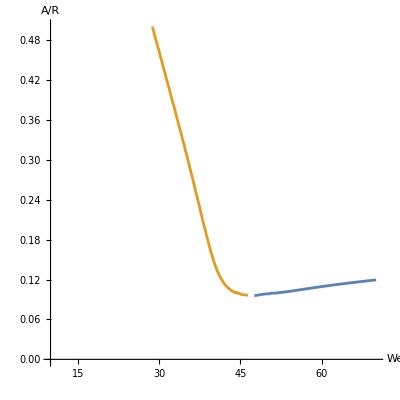

```mathematica
h31eqn[0.026,3]
```

```mathematica
dat
```

{0,1.57488,-34.2906,0,0.471291,0,0.,40,77/256}

```mathematica
h31eqn[oh_,kr_]:=(Clear[c0,d0,b312sol,we,wer,f31,zetak,delta,forc313];
k=kr;

wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
zetak=wer/we;
f31=Integrate[Cos[θ]*realkl[3,1]*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
b312sol=b312fun[0,kr];
k312ff=(-8.221763369944467 d31-0.1443169056666072 c31^2 d31-0.14431690566660715 d31^3) Cos[1. t]+(4.367651414978687 d31-0.6288442242191506 c31^2 d31+0.20961474140638348 d31^3) Cos[3. t]+c31 (12.362213675483725+0.14431690566660726 c31^2+0.14431690566660726 d31^2) Sin[1. t]+(-4.3676514149786865 c31+0.20961474140638356 c31^3-0.6288442242191506 c31 d31^2) Sin[3. t];
n312ff=(0.039387029625339576 c31^3+c31 (0.391945273924049+0.03938702962533969 d31^2)) Cos[t]+(-1.5933564791901642 c31+0.05560360416703505 c31^3+0.055603604167035046 c31 d31^2) Cos[1. t]-4.1315797859689365 c31 Cos[3. t]+0.22165679887412926 c31^3 Cos[3. t]-0.6649703966223879 c31 d31^2 Cos[3. t]+0.7376256523088051 d31 Sin[t]+0.03938702962533973 c31^2 d31 Sin[t]+0.039387029625339645 d31^3 Sin[t]+1.176937480676501 d31 Sin[1. t]+0.055603604167035046 c31^2 d31 Sin[1. t]+0.05560360416703505 d31^3 Sin[1. t]-4.131579785968941 d31 Sin[3. t]+0.6649703966223879 c31^2 d31 Sin[3. t]-0.22165679887412928 d31^3 Sin[3. t];
forc313=2*(Sin[t])*(kr+1)*(f31*b312sol)+2*(kr+1)*n312ff-2*D[k312ff,t](*-4*delta*(kr+1)(kr+2)*u311*)//TrigReduce;
fcos=Integrate[(1/Pi)*forc313*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forc313*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c31]-Coefficient[fsin,c31*d31^2]*d31^2//FullSimplify//Chop;g2=Coefficient[fsin,d31]-Coefficient[fsin,d31*c31^2]*c31^2//FullSimplify//Chop;g3=Coefficient[fcos,c31]-Coefficient[fcos,c31*d31^2]*d31^2//FullSimplify//Chop;g4=Coefficient[fcos,d31]-Coefficient[fcos,d31*c31^2]*c31^2//FullSimplify//Chop;
α=Coefficient[fcos,c31^3]//Chop;
β=Coefficient[fcos,d31^3]//Chop;

wer=(kr^2-1)(kr+2);
delta=oh/(√wer);dkr=delta*(kr+1)*(kr+2);
Δk=dkr;
dat={g1,g2,g3,g4,α,β,dkr,wer,f31};ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
)
```

```mathematica
dat
```

{0,1.57488,-34.2906,0,0.471291,0,0.0822192,40,77/256}

```mathematica
epssol[kr_,oh_,we_]:=(
wer=(kr^2-1)(kr+2);
zetak=wer/we;

allsol=Flatten[Join[{ϵ/.Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ],ϵ/.Solve[zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ]}]];
mainsol=Min[Select[allsol,Im[#]==0&&#>0&]]
)
```

```mathematica
h31list[oh_,kr_]:=(Clear[c0,d0,b312sol,we,wer,f31,zetak,delta,forc313];
k=kr;

wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
zetak=wer/we;
f31=Integrate[Cos[θ]*realkl[3,1]*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
b312sol=b312fun[0,kr];
k312ff=(-8.221763369944467 d31-0.1443169056666072 c31^2 d31-0.14431690566660715 d31^3) Cos[1. t]+(4.367651414978687 d31-0.6288442242191506 c31^2 d31+0.20961474140638348 d31^3) Cos[3. t]+c31 (12.362213675483725+0.14431690566660726 c31^2+0.14431690566660726 d31^2) Sin[1. t]+(-4.3676514149786865 c31+0.20961474140638356 c31^3-0.6288442242191506 c31 d31^2) Sin[3. t];
n312ff=(0.039387029625339576 c31^3+c31 (0.391945273924049+0.03938702962533969 d31^2)) Cos[t]+(-1.5933564791901642 c31+0.05560360416703505 c31^3+0.055603604167035046 c31 d31^2) Cos[1. t]-4.1315797859689365 c31 Cos[3. t]+0.22165679887412926 c31^3 Cos[3. t]-0.6649703966223879 c31 d31^2 Cos[3. t]+0.7376256523088051 d31 Sin[t]+0.03938702962533973 c31^2 d31 Sin[t]+0.039387029625339645 d31^3 Sin[t]+1.176937480676501 d31 Sin[1. t]+0.055603604167035046 c31^2 d31 Sin[1. t]+0.05560360416703505 d31^3 Sin[1. t]-4.131579785968941 d31 Sin[3. t]+0.6649703966223879 c31^2 d31 Sin[3. t]-0.22165679887412928 d31^3 Sin[3. t];
forc313=2*(Sin[t])*(kr+1)*(f31*b312sol)+2*(kr+1)*n312ff-2*D[k312ff,t](*-4*delta*(kr+1)(kr+2)*u311*)//TrigReduce;
fcos=Integrate[(1/Pi)*forc313*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forc313*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c31]-Coefficient[fsin,c31*d31^2]*d31^2//FullSimplify//Chop;g2=Coefficient[fsin,d31]-Coefficient[fsin,d31*c31^2]*c31^2//FullSimplify//Chop;g3=Coefficient[fcos,c31]-Coefficient[fcos,c31*d31^2]*d31^2//FullSimplify//Chop;g4=Coefficient[fcos,d31]-Coefficient[fcos,d31*c31^2]*c31^2//FullSimplify//Chop;
α=Coefficient[fcos,c31^3]//Chop;
β=Coefficient[fcos,d31^3]//Chop;

wer=(kr^2-1)(kr+2);
delta=oh/(√wer);dkr=delta*(kr+1)*(kr+2);
Δk=dkr;
dat={g1,g2,g3,g4,α,β,dkr,wer,f31};
list1=Table[{we,epssol[kr,oh,we]},{we,10,100,0.1}];
minwe=First[First[MinimalBy[list1,#[[2]]&]]];
ListLinePlot[list1,PlotRange->{{20,90},{0,0.5}}]
)
```

```mathematica
dat
```

{0,1.57488,-34.2906,0,0.471291,0,0.0822192,40,77/256}

```mathematica
fcos
```

0.+0.471291 c31^3+c31 (-34.2906+0.471291 d31^2)

```mathematica
fsin
```

0.+(1.57488+0.471291 c31^2) d31+0.471291 d31^3

```mathematica
Series[(1+x)^-1,{x,0,1}]
```

1-x+O[x]^2

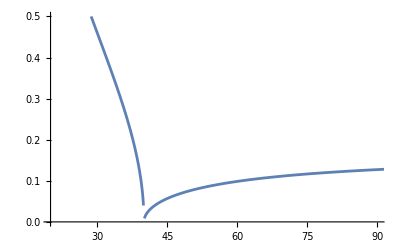

```mathematica
h31list[0.0,3]
```

```mathematica
fcos
```

0.+0.471291 c31^3+c31 (-34.2906+0.471291 d31^2)

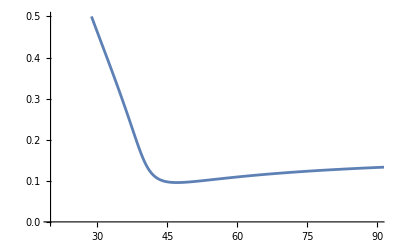

```mathematica
h31list[0.026,3]
```

```mathematica
fcos
```

0.+0.471291 c31^3+c31 (-34.2906+0.471291 d31^2)

```mathematica
fsin
```

0.+(1.57488+0.471291 c31^2) d31+0.471291 d31^3

```mathematica
dat
```

{0,1.57488,-34.2906,0,0.471291,0,0.0822192,40,77/256}

```mathematica
g3
```

-34.2906

```mathematica
1/(√α)*(-2*g3*(-g3*40))^(1/2)
```

446.76

```mathematica
fixedpointcos[kr_,we_,ϵ_]:=(solset={};Clear[ffun,gfun];detset={};solfin={};zetak=(kr^2-1)(kr+2)/we;
zetak2=(zetak-1)/ϵ^2;s=Δk/ϵ^2;sols={c0,d0}/.NSolve[{2*s*c0-zetak2*d0+g1*c0+g2*d0+(α*c0+β*d0)(c0^2+d0^2)==0,2*s*d0+zetak2*c0-g3*c0-g4*d0-(β*c0-α*d0)(c0^2+d0^2)==0},{c0,d0}];
For[jj=1,jj<Length[sols],jj++,If[Abs@Re@sols[[jj]][[1]]>0&&Abs@Re@sols[[jj]][[2]]>0&&Abs@Im@sols[[jj]][[1]]==0,AppendTo[solset,sols[[jj]]]]];
ffun[c0,d0]=-(2*s*c0-zetak2*d0+g1*c0+g2*d0+(α*c0+β*d0)(c0^2+d0^2));
gfun[c0,d0]=-(2*s*d0+zetak2*c0-g3*c0-g4*d0-(β*c0-α*d0)(c0^2+d0^2));
jacob={{,},{,}};
jacob[[1]][[1]]=D[ffun[c0,d0],c0];
jacob[[1]][[2]]=D[ffun[c0,d0],d0];
jacob[[2]][[1]]=D[gfun[c0,d0],c0];
jacob[[2]][[2]]=D[gfun[c0,d0],d0];
For[i=1,i<=Length[solset],i++,dete=Det[jacob]/.{c0->solset[[i]][[1]],d0->solset[[i]][[2]]};
tre=Tr[jacob]/.{c0->solset[[i]][[1]],d0->solset[[i]][[2]]};
(*If[dete>0,{AppendTo[solfin,solset[[i]]],AppendTo[detset,{tre,dete,tre^2-4dete}]}]*)
If[tre<0&&dete>0,{AppendTo[solfin,solset[[i]]],AppendTo[detset,{tre,dete,tre^2-4dete}]}]
];solfin
(*;
For[i=1,i<=Length@sols,i++,If[Abs[sols[[i]][[1]]]>0,solva=Abs[sols[[i]]];Break]];
solva*);res={};
AppendTo[res,Sqrt[(solfin[[1]][[2]])^2+(solfin[[1]][[1]])^2]];
AppendTo[res,ArcTan[solfin[[1]][[2]]/solfin[[1]][[1]]]];
If[res=={{},{}},res={0,0}]; (*if no res, no fixed point*)

(*evaluate the jacobian at (0,0)*)
tr=Tr[jacob]/.{c0->0,d0->0};
dtr=Det[jacob]/.{c0->0,d0->0};
(*If[tr<0&&dtr>0,res={0,0}];*)(*check if (0,0) is stable*);
If[tr<0&&dtr>0,res={0,0}]; (*(0,0) is a stable point if this condition holds*)
res (*the output will be 0 if (0,0) is a stable fixed point *)
)
```

```mathematica
fixedpointsin[kr_,we_,ϵ_]:=(solset={};Clear[ffun,gfun];detset={};solfin={};zetak=(kr^2-1)(kr+2)/we;
zetak2=(zetak-1)/ϵ^2;s=Δk/ϵ^2;sols={c0,d0}/.NSolve[{2*s*c0-zetak2*d0+g1*c0+g2*d0+(α*c0+β*d0)(c0^2+d0^2)==0,2*s*d0+zetak2*c0-g3*c0-g4*d0-(β*c0-α*d0)(c0^2+d0^2)==0},{c0,d0}];
For[jj=1,jj<Length[sols],jj++,If[Abs@Re@sols[[jj]][[1]]>0&&Abs@Re@sols[[jj]][[2]]>0&&Abs@Im@sols[[jj]][[1]]==0,AppendTo[solset,sols[[jj]]]]];
ffun[c0,d0]=-(2*s*c0-zetak2*d0+g1*c0+g2*d0+(α*c0+β*d0)(c0^2+d0^2));
gfun[c0,d0]=-(2*s*d0+zetak2*c0-g3*c0-g4*d0-(β*c0-α*d0)(c0^2+d0^2));
jacob={{,},{,}};
jacob[[1]][[1]]=D[ffun[c0,d0],c0];
jacob[[1]][[2]]=D[ffun[c0,d0],d0];
jacob[[2]][[1]]=D[gfun[c0,d0],c0];
jacob[[2]][[2]]=D[gfun[c0,d0],d0];
For[i=1,i<=Length[solset],i++,dete=Det[jacob]/.{c0->solset[[i]][[1]],d0->solset[[i]][[2]]};
tre=Tr[jacob]/.{c0->solset[[i]][[1]],d0->solset[[i]][[2]]};
(*If[dete>0,{AppendTo[solfin,solset[[i]]],AppendTo[detset,{tre,dete,tre^2-4dete}]}]*)
If[tre<0&&dete>0,{AppendTo[solfin,solset[[i]]],AppendTo[detset,{tre,dete,tre^2-4dete}]}]
];solfin
(*;
For[i=1,i<=Length@sols,i++,If[Abs[sols[[i]][[1]]]>0,solva=Abs[sols[[i]]];Break]];
solva*);res={};
AppendTo[res,Sqrt[(solfin[[1]][[2]])^2+(solfin[[1]][[1]])^2]];
AppendTo[res,ArcTan[solfin[[1]][[2]],solfin[[1]][[1]]]];
If[res=={{},{}},res={0,0}]; (*if no res, no fixed point*)

(*evaluate the jacobian at (0,0)*)
tr=Tr[jacob]/.{c0->0,d0->0};
dtr=Det[jacob]/.{c0->0,d0->0};
(*If[tr<0&&dtr>0,res={0,0}];*)(*check if (0,0) is stable*);
If[tr<0&&dtr>0,res={0,0}]; (*(0,0) is a stable point if this condition holds*)
res (*the output will be 0 if (0,0) is a stable fixed point *)
)
```

```mathematica
sols
```

{{0.-1.30254 ⅈ,0.-5.54536 ⅈ},{0.+1.30254 ⅈ,0.+5.54536 ⅈ},{0.273763,-1.1655},{-0.273763,1.1655},{0.,0.}}

```mathematica
Clear[s,Δk]
```

```mathematica
zetak=40/we;
zetak2=(zetak-1)/ϵ^2;s=Δk/ϵ^2;sols={c0,d0}/.NSolve[{2*s*c0-zetak2*d0+g1*c0+g2*d0+(α*c0+β*d0)(c0^2+d0^2)==0,2*s*d0+zetak2*c0-g3*c0-g4*d0-(β*c0-α*d0)(c0^2+d0^2)==0},{c0,d0}]//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Clear[s,zetak2,g1,g2,α,β,g3,g4]
```

```mathematica
dat
```

{0,1.57488,-34.2906,0,0.471291,0,0.0822192,40,77/256}

```mathematica
NSolve[{2*s*c0-zetak2*d0+g1*c0+g2*d0+(β*d0)(c0^2+d0^2)==0,2*s*d0+zetak2*c0-g3*c0-g4*d0-(β*c0)(c0^2+d0^2)==0},{c0,d0}]//FullSimplify
```

{{c0→0.,d0→0.}}

```mathematica
epssol[3,0.027,40]
```

0.149588

```mathematica
epssol[3,0.027,40]
```

0.149588

```mathematica
a31=fixedpoint[3,40.2,0.15]
```

{1.04427,-1.34511}

```mathematica
s
```

3.65419

```mathematica
Sqrt[0.29^2+1.366^2]
```

1.39644

```mathematica
solset
```

{{0.273763,-1.1655},{-0.273763,1.1655}}

```mathematica
jacob
```

{{-7.30838-0.942583 c0^2-0.471291 (c0^2+d0^2),-1.87533-0.942583 c0 d0},{-33.9901-0.942583 c0 d0,-7.30838-0.942583 d0^2-0.471291 (c0^2+d0^2)}}

```mathematica
bk0steady[oh_,bo_,ϵ_,we_,k_]:=((*kr=number of resonance mode, e.g., kr=3*)
delta=oh/(√we);Δk=delta*(k+1)*(k+2);
qk=Integrate[Cos[θ]*SphericalHarmonicY[k,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ζk=√(1/we(k^2-1)(k+2));
(*bkl0amp=(2 (1+k) qk (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)*)(*before forcing sign correction*)
bkl0amp=-(2 (1+k) qk (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)(*after forcing sign correction*)
)
```

```mathematica
Integrate[realklpt[]]
```

```mathematica
bk0steady[0.026,0,0.1,40,0]//N//FullSimplify
```

-0.0264298 Cos[t]-1.68764 Sin[t]

```mathematica
b201st[0.027,0,0.15,20]
```

2.0993+3.04519 Cos[2 t]-9.54706 Cos[t] Sin[t]

```mathematica
-0.026429757568093258 Cos[t]-1.6876373753328815 Sin[t]+0.15*(2.09930139587507+3.045190493519148 Cos[2 t]-9.547058157033977 Cos[t] Sin[t])
```

-0.0264298 Cos[t]-1.68764 Sin[t]+0.15 (2.0993+3.04519 Cos[2 t]-9.54706 Cos[t] Sin[t])

```mathematica
1.05*Cos[t+1.345]
```

1.05 Cos[1.345+t]

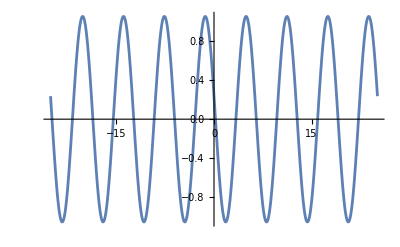

```mathematica
Plot[1.05 Cos[1.345+t],{t,-8 π,8 π}]
```

```mathematica
h31list[0.026,3];
```

```mathematica
5*10^-6*√(918/(0.0197*1.68*10^-3))
```

0.0263332

```mathematica
5*10^-6*√(918/(0.0197*2.28*10^-3))
```

0.0226043

```mathematica
Tan[Pi]
```

0

```mathematica
Table[fixedpoint[3,49,e],{e,0.1,0.3,0.02}]
```

{{1.70865,-0.729251},{3.61172,-0.886538},{4.15234,-0.985501},{4.36501,-1.0542},{4.44784,-1.10469},{4.47125,-1.14323},{4.46581,-1.17349},{4.44629,-1.19776},{4.42026,-1.21757},{4.39177,-1.23396},{4.36298,-1.24769}}

```mathematica
h31list[0.026,3];
```

```mathematica
epssol[3,0.026,45]
```

0.0974444

```mathematica
Table[fixedpoint[3,45,e],{e,0.1,0.3,0.02}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{0,0},{2.22334,-1.13395},{2.97513,-1.18277},{3.33035,-1.21721},{3.52939,-1.24252},{3.65108,-1.26169},{3.72989,-1.27657},{3.78318,-1.28834},{3.82046,-1.29781},{3.84729,-1.30555},{3.86707,-1.31194}}

```mathematica
h31list[0.026,3];a31=fixedpointcos[3,45,0.1]
```

{1.22234,-0.933859}

```mathematica
dat
```

{0,1.57488,-34.2906,0,0.471291,0,0.0822192,40,77/256}

```mathematica
Series[(e-1)^(-1/2),{e,0,1}]
```

Piecewise[{{-ⅈ-(ⅈ e)/2+O[e]^2, Im[e]≥0}, {ⅈ+(ⅈ e)/2+O[e]^2, True}}]

```mathematica
fixedpointcos[3,45,0.1]
```

{1.22234,-0.933859}

```mathematica
sols
```

{{0.-5.02107 ⅈ,0.-6.78712 ⅈ},{0.+5.02107 ⅈ,0.+6.78712 ⅈ},{0.726971,-0.982666},{-0.726971,0.982666},{0.,0.}}

```mathematica
bk0steady[0.0,0,0.1,45,0]//N//FullSimplify
```

-1.69703 Sin[t]

```mathematica
bk0steady[0.026,0,0.1,45,0]//N//FullSimplify
```

-0.0251846 Cos[t]-1.69666 Sin[t]

```mathematica
fff1=bk0steady[0.026,0,0.1,45,0]//N//FullSimplify
fff21=b201st[0.026,0,0.11,45]//N//FullSimplify
```

-0.0251846 Cos[t]-1.69666 Sin[t]

-9.14929+0.670797 Cos[2. t]-1.23118 Cos[t] Sin[t]

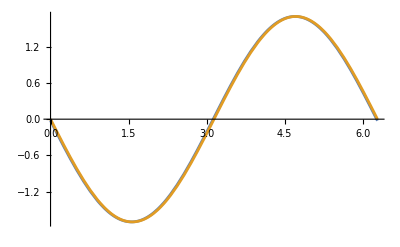

```mathematica
Plot[{fff1,fff},{t,0,2Pi}]
```

```mathematica
a31
```

{1.22234,-0.933859}

-9.25598+0.65808 Cos[2. t]-1.21194 Cos[t] Sin[t]

```mathematica
h31list[0.026,3];a31s=fixedpointsin[3,45,0.1]
```

{1.22234,2.50466}

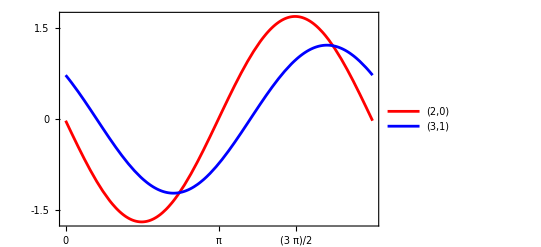

```mathematica
we402031=Plot[{ff+0.*ff2,Part[a31s,1]*Sin[t+Part[a31s,2]]},{t,0,2Pi},LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",18},PlotRange->All,Frame->True,PlotStyle->{Red,Blue},FrameTicks->{{{-1.5,0,1.5},{-1.5,0,1.5}},{{0,Pi/2,Pi,2Pi,3Pi/2,4Pi},{0,Pi/2,Pi,2Pi,3Pi/2,4Pi}}},PlotLegends->{"(2,0)","(3,1)"}]
```

```mathematica
we402031=Plot[{ff+0.*ff2,Part[a31s,1]*Sin[t+Part[a31s,2]+Pi]},{t,0,2Pi},LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",18},PlotRange->All,Frame->True,PlotStyle->{Red,Blue},FrameTicks->{{{-1.5,0,1.5},{-1.5,0,1.5}},{{0,Pi/2,Pi,2Pi,3Pi/2,4Pi},{0,Pi/2,Pi,2Pi,3Pi/2,4Pi}}},PlotLegends->{"(2,0)","(3,1)"}]
```

-Graphics-

```mathematica
h31list[0.026,3];a31c=fixedpointcos[3,45,0.1]
```

{1.22234,-0.933859}

```mathematica
we402031=Plot[{ff+0.*ff2,Part[a31c,1]*Cos[t-Part[a31c,2]]},{t,0,2Pi},LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",18},PlotRange->All,Frame->True,PlotStyle->{Red,Blue},FrameTicks->{{{-1.5,0,1.5},{-1.5,0,1.5}},{{0,Pi/2,Pi,2Pi,3Pi/2,4Pi},{0,Pi/2,Pi,2Pi,3Pi/2,4Pi}}},PlotLegends->{"(2,0)","(3,1)"}]
```

-Graphics-

```mathematica
Export["we402031.eps",we402031]
```

we402031.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["we402031.eps"]]]
```

```mathematica
Export["we402031_sim.eps",simamp]
```

we402031_sim.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["we402031_sim.eps"]]]
```

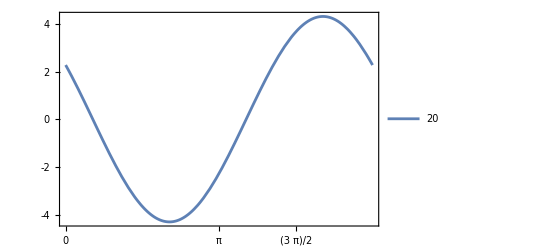

```mathematica
a31=fixedpoint[3,49.3,0.15];Plot[{(*ff,*)Part[a31,1]*Cos[t-Part[a31,2]]},{t,0,2Pi},LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",18},PlotRange->All,Frame->True,FrameTicks->{{{-4,-2,0,2,4},{-4,-2,0,2,4}},{{0,Pi/2,Pi,2Pi,3Pi/2,4Pi},{0,Pi/2,Pi,2Pi,3Pi/2,4Pi}}},PlotLegends->{"20","31"}]
```

```mathematica
g2
```

1.57488

```mathematica
g
```

```mathematica
dat
```

{0,1.57488,-34.2906,0,0.471291,0,0.0822192,40,77/256}

```mathematica
oh026=list1;
```

```mathematica
oh026panelb=list1;
```

```mathematica
oh01=list1;
```

```mathematica
oh0=list0;
```

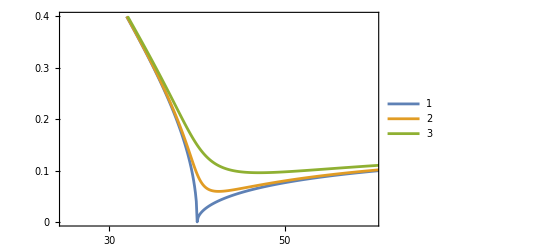

```mathematica
figfulloh=ListLinePlot[{oh0,oh01,oh026},PlotRange->{{25,60},{0,0.4}},PlotLegends->Automatic,PlotRange->All,LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",20},Frame->True,FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},{0,0.1,0.2,0.3,0.4,0.5}},{{10,20,30,40,50,60,70},{10,20,30,40,50,60,70}}}]
```

```mathematica
Export["fig_comparesim.eps",figfulloh]
```

fig_comparesim.eps

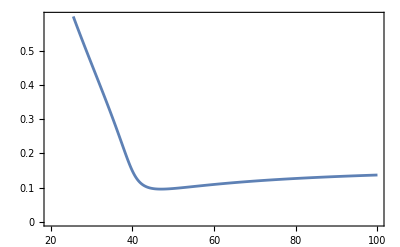

```mathematica
figcompred=ListLinePlot[{oh026panelb},PlotRange->{{20,100},{0,0.6}},PlotLegends->Automatic,PlotRange->All,LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",20},Frame->True,FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},{0,0.1,0.2,0.3,0.4,0.5}},{{20,30,40,50,60,70,80,90,100},{20,30,40,50,60,70,80,90,100}}}]
```

```mathematica
Export["fig_compwithred.eps",figcompred]
```

fig_compwithred.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fig_comparesim.eps"]]]
```

```mathematica
h31list[0.026,3]
```

-Graphics-

```mathematica
b201st[oh_,bo_,ϵ_,we_]:=(k=2;Clear[f1,f2,f3,f4,f5,Δk];

ff20=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];
ff24=Integrate[(SphericalHarmonicY[4,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];
p20f=p20st[oh,bo,ϵ,we];
forcing201=2*TrigReduce[(k+1)*(bk0steady[oh,bo,ϵ,we,2]*ff20+bk0steady[oh,bo,ϵ,we,4]*ff24)*Sin[t]-2*D[p20f,t]-4*delta*(k+1)(k+2)*p20f+2*(k+1)*r20st[oh,bo,ϵ,we]];
f1=Integrate[(1/(2Pi))*forcing201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*forcing201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*forcing201*Sin[2t],{t,-Pi,Pi}];
Δk=delta*(k+1)*(k+2);ζk=√((1/we)(k^2-1)(k+2)-(oh^2/we)(k+1)^2(k+2)^2);

b201sol=f1/(Δk^2+ζk^2)+((-4 f5 Δk+f4 (-4+Δk^2+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+Δk^2+ζk^2)) Sin[2 t])/(Δk^4+(-4+ζk^2)^2+2 Δk^2 (4+ζk^2))//TrigReduce//Simplify//Chop)
```

```mathematica
p20st[oh_,bo_,ϵ_,we_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];
b020=bk0steady[oh,bo,ϵ,we,2];
b040=bk0steady[oh,bo,ϵ,we,4];
b060=bk0steady[oh,bo,ϵ,we,6];
b060=0;
b020t=D[b020,t]//Simplify;
b040t=D[b040,t]//Simplify;
b060t=D[b060,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b040tt=D[b040,t,t]//Simplify;
b060tt=D[b060,t,t]//Simplify;
b031=b031t=b051=b051t=0;


p20f=0.2703356273593029 b020 b020t+0.17346536088888603 b031 b031t+0.08059851193539376 b020t b040+0.48359107161236264 b020 b040t+0.21299170640429924 b040 b040t+0.04771302630909682 b040t b060+0.0340807330779263 b040 b060t-0.10321905771900657 b060 b060t;
pklnow=p20f//TrigReduce//Chop)
```

```mathematica
r20st[oh_,bo_,ϵ_,we_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

b020=bk0steady[oh,bo,ϵ,we,2];
b040=bk0steady[oh,bo,ϵ,we,4];
b060=bk0steady[oh,bo,ϵ,we,6];
b060=0;
b020t=D[b020,t]//Simplify;
b040t=D[b040,t]//Simplify;
b060t=D[b060,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b040tt=D[b040,t,t]//Simplify;
b060tt=D[b060,t,t]//Simplify;
b031=b031t=b051=b051t=0;
wer=we;
r20f=0.06007458385762286 b020t^2+0.04927993207070625 b031t^2+0.063078313050504 b031 b031tt+0.12089776790309065 b020tt b040+0.06881270514600438 b040t^2+0.08191988707857663 b040 b040tt+0.11928256577274206 b040tt b060+0.10224219923377889 b040 b060t+0.1806278853130094 b040t b060t+0.06881270514600438 b060 b060t+0.052428727730289046 b060t^2+3.7846987830302403 b031 b031t delta+6.881270514600437 b040 b040t delta+10.019735524910333 b040t b060 delta+7.1569539463645215 b040 b060t delta+4.816889360220306 b060 b060t delta+b020t (0.20149627983848442 b040t+3.6044750314573717 b020 delta+4.835910716123625 b040 delta)+b020 (0.0901118757864343 b020tt+0.12089776790309065 b040tt+10.155412503859615 b040t delta+(5.803092859348351 b040)/wer)+(0.9011187578643429 b020^2)/wer+(1.387722887111088 b031^2)/wer+(3.112955708985912 b040^2)/wer+(4.532737499364197 b040 b060)/wer;
rklnow=r20f//TrigReduce//Chop)
```

```mathematica
list0={{10.,1.3801825496839124},{10.1,1.3710421673447677},{10.2,1.3620214616789839},{10.3,1.353117519328622},{10.4,1.3443275242589092},{10.5,1.3356487535886712},{10.6,1.327078573637052},{10.7,1.3186144361733776},{10.8,1.3102538748579162},{10.9,1.3019945018621584},{11.,1.2938340046579857},{11.1,1.2857701429658466},{11.2,1.2778007458526943},{11.3,1.2699237089710718},{11.4,1.262136991931291},{11.5,1.2544386157991796},{11.6,1.246826660712352},{11.7,1.2392992636084215},{11.8,1.2318546160589807},{11.9,1.2244909622035718},{12.,1.2172065967782268},{12.1,1.2099998632334963},{12.2,1.2028691519371961},{12.3,1.1958128984573937},{12.4,1.1888295819214263},{12.5,1.181917723446993},{12.6,1.1750758846416065},{12.7,1.168302666166898},{12.8,1.1615967063644865},{12.9,1.1549566799403037},{13.,1.148381296704455},{13.1,1.1418693003638576},{13.2,1.1354194673650553},{13.3,1.1290306057847577},{13.4,1.122701554265788},{13.5,1.1164311809962502},{13.6,1.1102183827298504},{13.7,1.1040620838454198},{13.8,1.0979612354437869},{13.9,1.091914814480259},{14.,1.0859218229310503},{14.100000000000001,1.0799812869920973},{14.2,1.0740922563087727},{14.3,1.0682538032350961},{14.4,1.0624650221211078},{14.5,1.0567250286271381},{14.600000000000001,1.0510329590637804},{14.7,1.0453879697564232},{14.8,1.0397892364332677},{14.9,1.0342359536357983},{15.,1.0287273341507364},{15.100000000000001,1.0232626084625498},{15.2,1.017841024225637},{15.3,1.012461845755349},{15.4,1.00712435353705},{15.5,1.0018278437524646},{15.600000000000001,0.9965716278225814},{15.7,0.9913550319664315},{15.8,0.9861773967750859},{15.9,0.9810380768002461},{16.,0.9759364401568335},{16.1,0.9708718681390124},{16.2,0.9658437548491027},{16.3,0.9608515068388667},{16.4,0.9558945427626799},{16.5,0.9509722930421113},{16.6,0.9460841995414663},{16.7,0.9412297152538649},{16.8,0.936408303997438},{16.9,0.9316194401212607},{17.,0.926862608220637},{17.1,0.9221373028613846},{17.2,0.9174430283127746},{17.3,0.9127792982887961},{17.4,0.9081456356974362},{17.5,0.9035415723976683},{17.6,0.8989666489638685},{17.7,0.8944204144573754},{17.8,0.8899024262049364},{17.9,0.8854122495837826},{18.,0.8809494578130912},{18.1,0.8765136317516007},{18.200000000000003,0.8721043597011581},{18.3,0.8677212372159793},{18.4,0.8633638669174215},{18.5,0.8590318583140657},{18.6,0.8547248276269225},{18.700000000000003,0.8504423976195774},{18.8,0.8461841974330991},{18.9,0.8419498624255446},{19.,0.8377390340158977},{19.1,0.8335513595322867},{19.200000000000003,0.8293864920643285},{19.3,0.8252440903194559},{19.4,0.8211238184830935},{19.5,0.8170253460825398},{19.6,0.8129483478544378},{19.700000000000003,0.8088925036156989},{19.8,0.8048574981377683},{19.9,0.8008430210241145},{20.,0.7968487665908308},{20.1,0.7928744337502426},{20.200000000000003,0.7889197258974163},{20.3,0.7849843507994713},{20.4,0.7810680204875973},{20.5,0.7771704511516843},{20.6,0.7732913630374763},{20.700000000000003,0.7694304803461594},{20.8,0.7655875311363032},{20.9,0.7617622472280707},{21.,0.7579543641096216},{21.1,0.7541636208456297},{21.200000000000003,0.7503897599878426},{21.3,0.7466325274876103},{21.4,0.742891672610316},{21.5,0.7391669478516377},{21.6,0.7354581088555812},{21.700000000000003,0.7317649143342129},{21.8,0.7280871259890402},{21.9,0.7244245084339714},{22.,0.720776829119802},{22.1,0.7171438582601678},{22.200000000000003,0.7135253687589127},{22.3,0.7099211361388136},{22.4,0.7063309384716109},{22.5,0.7027545563092976},{22.6,0.6991917726166101},{22.700000000000003,0.6956423727046772},{22.8,0.6921061441657773},{22.9,0.6885828768091563},{23.,0.6850723625978622},{23.1,0.6815743955865501},{23.200000000000003,0.6780887718602137},{23.3,0.6746152894738002},{23.4,0.6711537483926643},{23.5,0.6677039504338227},{23.6,0.664265699207964},{23.700000000000003,0.660838800062174},{23.8,0.6574230600233386},{23.9,0.6540182877421801},{24.,0.650624293437889},{24.1,0.6472408888433158},{24.200000000000003,0.6438678871506758},{24.3,0.6405051029577357},{24.4,0.6371523522144373},{24.5,0.6338094521699265},{24.6,0.6304762213199419},{24.700000000000003,0.6271524793545277},{24.8,0.6238380471060355},{24.9,0.6205327464973694},{25.,0.6172364004904418},{25.1,0.6139488330347965},{25.200000000000003,0.6106698690163637},{25.3,0.6073993342063012},{25.4,0.6041370552098894},{25.5,0.6008828594154315},{25.6,0.5976365749431232},{25.700000000000003,0.5943980305938472},{25.8,0.5911670557978516},{25.9,0.5879434805632653},{26.,0.5847271354244119},{26.1,0.5815178513898697},{26.2,0.578315459890239},{26.3,0.5751197927255608},{26.400000000000002,0.5719306820123471},{26.5,0.568747960130165},{26.6,0.5655714596677277},{26.7,0.5624010133684374},{26.8,0.5592364540753256},{26.900000000000002,0.5560776146753358},{27.,0.5529243280428857},{27.1,0.5497764269826537},{27.2,0.5466337441715231},{27.3,0.5434961120996193},{27.400000000000002,0.5403633630103738},{27.5,0.5372353288395423},{27.6,0.5341118411531045},{27.7,0.5309927310839692},{27.8,0.5278778292674026},{27.900000000000002,0.5247669657751005},{28.,0.5216599700478114},{28.1,0.5185566708264236},{28.2,0.5154568960814174},{28.3,0.5123604729405842},{28.400000000000002,0.5092672276149043},{28.5,0.5061769853224759},{28.6,0.5030895702103746},{28.7,0.5000048052743242},{28.8,0.4969225122760478},{28.900000000000002,0.4938425116581625},{29.,0.49076462245647734},{29.1,0.4876886622095368},{29.200000000000003,0.48461444686525673},{29.3,0.48154179068447583},{29.400000000000002,0.47847050614124986},{29.5,0.47540040381969645},{29.6,0.47233129230718424},{29.700000000000003,0.46926297808366363},{29.8,0.4661952654069006},{29.900000000000002,0.46312795619338304},{30.,0.4600608498946374},{30.1,0.45699374336868614},{30.200000000000003,0.4539264307463561},{30.3,0.4508587032921293},{30.400000000000002,0.447790349259207},{30.5,0.4447211537384371},{30.6,0.44165089850072714},{30.700000000000003,0.4385793618325474},{30.8,0.43550631836409237},{30.900000000000002,0.4324315388896402},{31.,0.4293547901796277},{31.1,0.42627583478390446},{31.200000000000003,0.42319443082560826},{31.3,0.42011033178505397},{31.400000000000002,0.4170232862729826},{31.5,0.41393303779247254},{31.6,0.41083932448875726},{31.700000000000003,0.4077418788861367},{31.8,0.40464042761110575},{31.900000000000002,0.4015346911007541},{32.,0.3984243832954154},{32.1,0.3953092113144582},{32.2,0.3921888751140243},{32.3,0.38906306712541483},{32.400000000000006,0.38593147187271776},{32.5,0.3827937655681517},{32.6,0.3796496156834563},{32.7,0.37649868049553314},{32.8,0.37334060860435775},{32.900000000000006,0.3701750384210162},{33.,0.36700159762352697},{33.1,0.36381990257786795},{33.2,0.36062955772141625},{33.3,0.35743015490570873},{33.400000000000006,0.3542212726951494},{33.5,0.35100247561794967},{33.6,0.34777331336520767},{33.7,0.3445333199336251},{33.8,0.34128201270688363},{33.900000000000006,0.3380188914701789},{34.,0.33474343735182743},{34.1,0.3314551116851807},{34.2,0.3281533547833548},{34.3,0.32483758461840934},{34.400000000000006,0.3215071953956753},{34.5,0.3181615560128245},{34.6,0.3148000083920412},{34.7,0.3114218656722502},{34.8,0.3080264102467286},{34.900000000000006,0.3046128916295971},{35.,0.301180524132556},{35.1,0.29772848433078464},{35.2,0.2942559082941229},{35.3,0.29076188855637225},{35.400000000000006,0.2872454707917728},{35.5,0.28370565016331795},{35.6,0.28014136730238876},{35.7,0.2765515038731921},{35.8,0.27293487766836083},{35.900000000000006,0.2692902371737163},{36.,0.265616255530277},{36.1,0.26191152380978805},{36.2,0.25817454350598956},{36.3,0.25440371812693224},{36.400000000000006,0.2505973437533192},{36.5,0.24675359840324365},{36.6,0.24287053001373107},{36.7,0.23894604281290158},{36.8,0.23497788181153853},{36.900000000000006,0.23096361508717883},{37.,0.22690061346456125},{37.1,0.22278602710944173},{37.2,0.21861675844333617},{37.3,0.2143894306475306},{37.400000000000006,0.21010035084645498},{37.5,0.20574546683014724},{37.6,0.20132031587518628},{37.7,0.19681996382803577},{37.8,0.19223893208851436},{37.900000000000006,0.18757110942291214},{38.,0.18280964457128734},{38.1,0.1779468142807709},{38.2,0.17297385952911362},{38.3,0.16788078004291865},{38.400000000000006,0.16265607335947196},{38.5,0.15728639898151178},{38.6,0.15175613956255266},{38.7,0.14604681772645337},{38.8,0.14013630590059037},{38.900000000000006,0.13399773167890386},{39.,0.12759792185605032},{39.1,0.1208951228113876},{39.2,0.11383553808440385},{39.3,0.1063478341399713},{39.400000000000006,0.09833393510977008},{39.5,0.08965249061591714},{39.6,0.08008631434664491},{39.7,0.06926937653153797},{39.8,0.056487111387032184},{39.900000000000006,0.03989233495313577},{40.,0},{40.1,0.008527870210359301},{40.2,0.012045220083782435},{40.3,0.014734007025548492},{40.400000000000006,0.016992296653092844},{40.5,0.018974496431196804},{40.6,0.0207599057132948},{40.7,0.02239569702997178},{40.8,0.023912648511358794},{40.900000000000006,0.025332168552543364},{41.,0.026669866388417368},{41.1,0.02793754242320101},{41.2,0.029144377482479923},{41.3,0.030297683091834456},{41.400000000000006,0.031403395990203045},{41.5,0.03246641603083678},{41.6,0.03349084415651621},{41.7,0.03448015436932675},{41.8,0.03543732079029184},{41.900000000000006,0.0363649133692566},{42.,0.037265171215555136},{42.1,0.03814005963474574},{42.2,0.03899131509218393},{42.300000000000004,0.039820481089462276},{42.4,0.04062893710400241},{42.5,0.041417922165209786},{42.6,0.042188554235289596},{42.7,0.04294184627344359},{42.800000000000004,0.043678719652497956},{42.9,0.04440001544305322},{43.,0.04510650396578266},{43.1,0.04579889292643544},{43.2,0.04647783438269252},{43.300000000000004,0.04714393074182767},{43.4,0.04779773994925556},{43.5,0.048439779997687726},{43.6,0.04907053286271502},{43.7,0.049690447951679255},{43.800000000000004,0.05029994513755238},{43.9,0.05089941743736858},{44.,0.05148923338490499},{44.1,0.05206973913929101},{44.2,0.05264126036466867},{44.300000000000004,0.05320410391062956},{44.4,0.05375855931869398},{44.5,0.054304900176393396},{44.6,0.05484338533742296},{44.7,0.055374260023744064},{44.800000000000004,0.05589775682333269},{44.9,0.05641409659543006},{45.,0.056923489293590264},{45.1,0.05742613471549006},{45.2,0.05792222318733166},{45.300000000000004,0.0584119361896985},{45.4,0.058895446930886344},{45.5,0.05937292087301506},{45.6,0.05984451621560098},{45.7,0.06031038434073269},{45.800000000000004,0.06077067022352294},{45.9,0.061225512811100155},{46.,0.061675045373047646},{46.1,0.06211939582588356},{46.2,0.06255868703390279},{46.300000000000004,0.06299303708845806},{46.4,0.06342255956754622},{46.5,0.06384736377737694},{46.6,0.06426755497743451},{46.7,0.06468323459039566},{46.800000000000004,0.06509450039813557},{46.9,0.06550144672493655},{47.,0.06590416460891022},{47.1,0.06630274196255022},{47.2,0.06669726372324997},{47.300000000000004,0.06708781199454468},{47.4,0.06747446617876936},{47.5,0.06785730310176534},{47.6,0.06823639713021212},{47.7,0.0686118202821134},{47.800000000000004,0.06898364233092143},{47.9,0.06935193090374345},{48.,0.06971675157403874},{48.1,0.07007816794918038},{48.2,0.07043624175322773},{48.300000000000004,0.07079103290522684},{48.400000000000006,0.07114259959333251},{48.5,0.07149099834502241},{48.6,0.07183628409365385},{48.7,0.07217851024159422},{48.800000000000004,0.07251772872013938},{48.900000000000006,0.07285399004641914},{49.,0.07318734337747325},{49.1,0.07351783656166924},{49.2,0.07384551618762143},{49.300000000000004,0.07417042763075757},{49.400000000000006,0.07449261509767229},{49.5,0.07481212166839386},{49.6,0.07512898933668516},{49.7,0.07544325904848834},{49.800000000000004,0.07575497073861914},{49.900000000000006,0.07606416336580667},{50.,0.0763708749461696},{50.1,0.07667514258521459},{50.2,0.07697700250843502},{50.300000000000004,0.07727649009058615},{50.400000000000006,0.07757363988370511},{50.5,0.07786848564394225},{50.6,0.078161060357265},{50.7,0.07845139626409157},{50.800000000000004,0.07873952488290982},{50.900000000000006,0.07902547703293103},{51.,0.07930928285582786},{51.1,0.07959097183660079},{51.2,0.07987057282361604},{51.300000000000004,0.0801481140478552},{51.400000000000006,0.08042362314141402},{51.5,0.08069712715528668},{51.6,0.08096865257646856},{51.7,0.08123822534441012},{51.800000000000004,0.0815058708668511},{51.900000000000006,0.0817716140350645},{52.,0.0820354792385363},{52.1,0.08229749037910718},{52.2,0.08255767088459974},{52.300000000000004,0.08281604372195446},{52.400000000000006,0.08307263140989589},{52.5,0.0833274560311497},{52.6,0.08358053924422991},{52.7,0.08383190229481481},{52.800000000000004,0.08408156602672937},{52.900000000000006,0.08432955089255019},{53.,0.08457587696384984},{53.1,0.0848205639410943},{53.2,0.08506363116320911},{53.300000000000004,0.0853050976168268},{53.400000000000006,0.08554498194522933},{53.5,0.08578330245699735},{53.6,0.08602007713437843},{53.7,0.08625532364138486},{53.800000000000004,0.08648905933163241},{53.900000000000006,0.08672130125592988},{54.,0.08695206616962861},{54.1,0.0871813705397426},{54.2,0.08740923055184624},{54.300000000000004,0.08763566211675979},{54.400000000000006,0.08786068087702938},{54.5,0.08808430221321},{54.6,0.08830654124995868},{54.7,0.08852741286194446},{54.800000000000004,0.08874693167958238},{54.900000000000006,0.08896511209459781},{55.,0.08918196826542713},{55.1,0.08939751412246061},{55.2,0.0896117633731335},{55.300000000000004,0.08982472950687015},{55.400000000000006,0.09003642579988695},{55.5,0.09024686531985868},{55.6,0.09045606093045284},{55.7,0.09066402529573726},{55.800000000000004,0.09087077088446441},{55.900000000000006,0.09107630997423737},{56.,0.0912806546555612},{56.1,0.09148381683578323},{56.2,0.09168580824292684},{56.300000000000004,0.0918866404294212},{56.400000000000006,0.09208632477573156},{56.5,0.09228487249389211},{56.6,0.09248229463094597},{56.7,0.09267860207229396},{56.800000000000004,0.09287380554495614},{56.900000000000006,0.09306791562074845},{57.,0.09326094271937713},{57.1,0.09345289711145367},{57.2,0.09364378892143287},{57.300000000000004,0.09383362813047601},{57.400000000000006,0.09402242457924215},{57.5,0.09421018797060893},{57.6,0.09439692787232586},{57.7,0.09458265371960166},{57.800000000000004,0.09476737481762768},{57.900000000000006,0.0949511003440397},{58.,0.09513383935131933},{58.1,0.09531560076913781},{58.2,0.0954963934066425},{58.300000000000004,0.09567622595468915},{58.400000000000006,0.0958551069880209},{58.5,0.09603304496739531},{58.6,0.09621004824166161},{58.7,0.09638612504978891},{58.800000000000004,0.09656128352284736},{58.900000000000006,0.09673553168594319},{59.,0.09690887746010932},{59.1,0.0970813286641523},{59.2,0.0972528930164574},{59.300000000000004,0.09742357813675233},{59.400000000000006,0.09759339154783161},{59.5,0.09776234067724184},{59.6,0.0979304328589293},{59.7,0.09809767533485127},{59.800000000000004,0.09826407525655119},{59.900000000000006,0.09842963968669967},{60.,0.09859437560060139},{60.1,0.09875828988766934},{60.2,0.09892138935286705},{60.300000000000004,0.09908368071811978},{60.400000000000006,0.09924517062369535},{60.5,0.09940586562955558},{60.6,0.09956577221667896},{60.7,0.09972489678835524},{60.800000000000004,0.09988324567145306},{60.900000000000006,0.10004082511766078},{61.,0.10019764130470164},{61.1,0.10035370033752367},{61.2,0.10050900824946482},{61.300000000000004,0.10066357100339463},{61.400000000000006,0.10081739449283207},{61.5,0.100970484543041},{61.6,0.10112284691210337},{61.7,0.1012744872919705},{61.800000000000004,0.10142541130949377},{61.900000000000006,0.10157562452743424},{62.,0.10172513244545263},{62.1,0.10187394050107937},{62.2,0.10202205407066575},{62.300000000000004,0.10216947847031635},{62.400000000000006,0.10231621895680322},{62.5,0.1024622807284625},{62.6,0.10260766892607345},{62.7,0.10275238863372065},{62.800000000000004,0.10289644487963971},{62.900000000000006,0.10303984263704685},{63.,0.10318258682495263},{63.1,0.10332468230896028},{63.2,0.10346613390204915},{63.300000000000004,0.10360694636534322},{63.400000000000006,0.10374712440886555},{63.5,0.10388667269227836},{63.6,0.10402559582560976},{63.7,0.10416389836996676},{63.800000000000004,0.1043015848382354},{63.900000000000006,0.10443865969576806},{64.,0.10457512736105809},{64.1,0.1047109922064025},{64.2,0.10484625855855231},{64.30000000000001,0.1049809306993516},{64.4,0.10511501286636477},{64.5,0.10524850925349287},{64.6,0.10538142401157885},{64.7,0.10551376124900215},{64.80000000000001,0.10564552503226277},{64.9,0.10577671938655508},{65.,0.10590734829633179},{65.1,0.10603741570585781},{65.2,0.10616692551975473},{65.30000000000001,0.10629588160353577},{65.4,0.10642428778413159},{65.5,0.10655214785040709},{65.6,0.10667946555366942},{65.7,0.10680624460816722},{65.80000000000001,0.10693248869158152},{65.9,0.10705820144550834},{66.,0.10718338647593326},{66.1,0.10730804735369776},{66.2,0.10743218761495822},{66.30000000000001,0.1075558107616368},{66.4,0.10767892026186524},{66.5,0.10780151955042128},{66.6,0.10792361202915772},{66.7,0.1080452010674246},{66.80000000000001,0.10816629000248454},{66.9,0.10828688213992112},{67.,0.10840698075404095},{67.1,0.10852658908826902},{67.2,0.10864571035553783},{67.30000000000001,0.10876434773867008},{67.4,0.10888250439075561},{67.5,0.10900018343552204},{67.6,0.10911738796769967},{67.7,0.10923412105338058},{67.80000000000001,0.10935038573037213},{67.9,0.10946618500854484},{68.,0.10958152187017493},{68.1,0.10969639927028156},{68.2,0.1098108201369586},{68.30000000000001,0.10992478737170154},{68.4,0.11003830384972929},{68.5,0.110151372420301},{68.6,0.11026399590702801},{68.7,0.11037617710818118},{68.80000000000001,0.11048791879699336},{68.9,0.11059922372195748},{69.,0.11071009460711996},{69.1,0.11082053415236989},{69.2,0.11093054503372377},{69.30000000000001,0.11104012990360584},{69.4,0.11114929139112471},{69.5,0.11125803210234539},{69.6,0.11136635462055747},{69.7,0.1114742615065395},{69.80000000000001,0.11158175529881932},{69.9,0.1116888385139305},{70.,0.11179551364666535}};
```

```mathematica
list00={{10.,1.3801825496839124},{10.1,1.3710421673447677},{10.2,1.3620214616789839},{10.3,1.353117519328622},{10.4,1.3443275242589092},{10.5,1.3356487535886712},{10.6,1.327078573637052},{10.7,1.3186144361733776},{10.8,1.3102538748579162},{10.9,1.3019945018621584},{11.,1.2938340046579857},{11.1,1.2857701429658466},{11.2,1.2778007458526943},{11.3,1.2699237089710718},{11.4,1.262136991931291},{11.5,1.2544386157991796},{11.6,1.246826660712352},{11.7,1.2392992636084215},{11.8,1.2318546160589807},{11.9,1.2244909622035718},{12.,1.2172065967782268},{12.1,1.2099998632334963},{12.2,1.2028691519371961},{12.3,1.1958128984573937},{12.4,1.1888295819214263},{12.5,1.181917723446993},{12.6,1.1750758846416065},{12.7,1.168302666166898},{12.8,1.1615967063644865},{12.9,1.1549566799403037},{13.,1.148381296704455},{13.1,1.1418693003638576},{13.2,1.1354194673650553},{13.3,1.1290306057847577},{13.4,1.122701554265788},{13.5,1.1164311809962502},{13.6,1.1102183827298504},{13.7,1.1040620838454198},{13.8,1.0979612354437869},{13.9,1.091914814480259},{14.,1.0859218229310503},{14.100000000000001,1.0799812869920973},{14.2,1.0740922563087727},{14.3,1.0682538032350961},{14.4,1.0624650221211078},{14.5,1.0567250286271381},{14.600000000000001,1.0510329590637804},{14.7,1.0453879697564232},{14.8,1.0397892364332677},{14.9,1.0342359536357983},{15.,1.0287273341507364},{15.100000000000001,1.0232626084625498},{15.2,1.017841024225637},{15.3,1.012461845755349},{15.4,1.00712435353705},{15.5,1.0018278437524646},{15.600000000000001,0.9965716278225814},{15.7,0.9913550319664315},{15.8,0.9861773967750859},{15.9,0.9810380768002461},{16.,0.9759364401568335},{16.1,0.9708718681390124},{16.2,0.9658437548491027},{16.3,0.9608515068388667},{16.4,0.9558945427626799},{16.5,0.9509722930421113},{16.6,0.9460841995414663},{16.7,0.9412297152538649},{16.8,0.936408303997438},{16.9,0.9316194401212607},{17.,0.926862608220637},{17.1,0.9221373028613846},{17.2,0.9174430283127746},{17.3,0.9127792982887961},{17.4,0.9081456356974362},{17.5,0.9035415723976683},{17.6,0.8989666489638685},{17.7,0.8944204144573754},{17.8,0.8899024262049364},{17.9,0.8854122495837826},{18.,0.8809494578130912},{18.1,0.8765136317516007},{18.200000000000003,0.8721043597011581},{18.3,0.8677212372159793},{18.4,0.8633638669174215},{18.5,0.8590318583140657},{18.6,0.8547248276269225},{18.700000000000003,0.8504423976195774},{18.8,0.8461841974330991},{18.9,0.8419498624255446},{19.,0.8377390340158977},{19.1,0.8335513595322867},{19.200000000000003,0.8293864920643285},{19.3,0.8252440903194559},{19.4,0.8211238184830935},{19.5,0.8170253460825398},{19.6,0.8129483478544378},{19.700000000000003,0.8088925036156989},{19.8,0.8048574981377683},{19.9,0.8008430210241145},{20.,0.7968487665908308},{20.1,0.7928744337502426},{20.200000000000003,0.7889197258974163},{20.3,0.7849843507994713},{20.4,0.7810680204875973},{20.5,0.7771704511516843},{20.6,0.7732913630374763},{20.700000000000003,0.7694304803461594},{20.8,0.7655875311363032},{20.9,0.7617622472280707},{21.,0.7579543641096216},{21.1,0.7541636208456297},{21.200000000000003,0.7503897599878426},{21.3,0.7466325274876103},{21.4,0.742891672610316},{21.5,0.7391669478516377},{21.6,0.7354581088555812},{21.700000000000003,0.7317649143342129},{21.8,0.7280871259890402},{21.9,0.7244245084339714},{22.,0.720776829119802},{22.1,0.7171438582601678},{22.200000000000003,0.7135253687589127},{22.3,0.7099211361388136},{22.4,0.7063309384716109},{22.5,0.7027545563092976},{22.6,0.6991917726166101},{22.700000000000003,0.6956423727046772},{22.8,0.6921061441657773},{22.9,0.6885828768091563},{23.,0.6850723625978622},{23.1,0.6815743955865501},{23.200000000000003,0.6780887718602137},{23.3,0.6746152894738002},{23.4,0.6711537483926643},{23.5,0.6677039504338227},{23.6,0.664265699207964},{23.700000000000003,0.660838800062174},{23.8,0.6574230600233386},{23.9,0.6540182877421801},{24.,0.650624293437889},{24.1,0.6472408888433158},{24.200000000000003,0.6438678871506758},{24.3,0.6405051029577357},{24.4,0.6371523522144373},{24.5,0.6338094521699265},{24.6,0.6304762213199419},{24.700000000000003,0.6271524793545277},{24.8,0.6238380471060355},{24.9,0.6205327464973694},{25.,0.6172364004904418},{25.1,0.6139488330347965},{25.200000000000003,0.6106698690163637},{25.3,0.6073993342063012},{25.4,0.6041370552098894},{25.5,0.6008828594154315},{25.6,0.5976365749431232},{25.700000000000003,0.5943980305938472},{25.8,0.5911670557978516},{25.9,0.5879434805632653},{26.,0.5847271354244119},{26.1,0.5815178513898697},{26.2,0.578315459890239},{26.3,0.5751197927255608},{26.400000000000002,0.5719306820123471},{26.5,0.568747960130165},{26.6,0.5655714596677277},{26.7,0.5624010133684374},{26.8,0.5592364540753256},{26.900000000000002,0.5560776146753358},{27.,0.5529243280428857},{27.1,0.5497764269826537},{27.2,0.5466337441715231},{27.3,0.5434961120996193},{27.400000000000002,0.5403633630103738},{27.5,0.5372353288395423},{27.6,0.5341118411531045},{27.7,0.5309927310839692},{27.8,0.5278778292674026},{27.900000000000002,0.5247669657751005},{28.,0.5216599700478114},{28.1,0.5185566708264236},{28.2,0.5154568960814174},{28.3,0.5123604729405842},{28.400000000000002,0.5092672276149043},{28.5,0.5061769853224759},{28.6,0.5030895702103746},{28.7,0.5000048052743242},{28.8,0.4969225122760478},{28.900000000000002,0.4938425116581625},{29.,0.49076462245647734},{29.1,0.4876886622095368},{29.200000000000003,0.48461444686525673},{29.3,0.48154179068447583},{29.400000000000002,0.47847050614124986},{29.5,0.47540040381969645},{29.6,0.47233129230718424},{29.700000000000003,0.46926297808366363},{29.8,0.4661952654069006},{29.900000000000002,0.46312795619338304},{30.,0.4600608498946374},{30.1,0.45699374336868614},{30.200000000000003,0.4539264307463561},{30.3,0.4508587032921293},{30.400000000000002,0.447790349259207},{30.5,0.4447211537384371},{30.6,0.44165089850072714},{30.700000000000003,0.4385793618325474},{30.8,0.43550631836409237},{30.900000000000002,0.4324315388896402},{31.,0.4293547901796277},{31.1,0.42627583478390446},{31.200000000000003,0.42319443082560826},{31.3,0.42011033178505397},{31.400000000000002,0.4170232862729826},{31.5,0.41393303779247254},{31.6,0.41083932448875726},{31.700000000000003,0.4077418788861367},{31.8,0.40464042761110575},{31.900000000000002,0.4015346911007541},{32.,0.3984243832954154},{32.1,0.3953092113144582},{32.2,0.3921888751140243},{32.3,0.38906306712541483},{32.400000000000006,0.38593147187271776},{32.5,0.3827937655681517},{32.6,0.3796496156834563},{32.7,0.37649868049553314},{32.8,0.37334060860435775},{32.900000000000006,0.3701750384210162},{33.,0.36700159762352697},{33.1,0.36381990257786795},{33.2,0.36062955772141625},{33.3,0.35743015490570873},{33.400000000000006,0.3542212726951494},{33.5,0.35100247561794967},{33.6,0.34777331336520767},{33.7,0.3445333199336251},{33.8,0.34128201270688363},{33.900000000000006,0.3380188914701789},{34.,0.33474343735182743},{34.1,0.3314551116851807},{34.2,0.3281533547833548},{34.3,0.32483758461840934},{34.400000000000006,0.3215071953956753},{34.5,0.3181615560128245},{34.6,0.3148000083920412},{34.7,0.3114218656722502},{34.8,0.3080264102467286},{34.900000000000006,0.3046128916295971},{35.,0.301180524132556},{35.1,0.29772848433078464},{35.2,0.2942559082941229},{35.3,0.29076188855637225},{35.400000000000006,0.2872454707917728},{35.5,0.28370565016331795},{35.6,0.28014136730238876},{35.7,0.2765515038731921},{35.8,0.27293487766836083},{35.900000000000006,0.2692902371737163},{36.,0.265616255530277},{36.1,0.26191152380978805},{36.2,0.25817454350598956},{36.3,0.25440371812693224},{36.400000000000006,0.2505973437533192},{36.5,0.24675359840324365},{36.6,0.24287053001373107},{36.7,0.23894604281290158},{36.8,0.23497788181153853},{36.900000000000006,0.23096361508717883},{37.,0.22690061346456125},{37.1,0.22278602710944173},{37.2,0.21861675844333617},{37.3,0.2143894306475306},{37.400000000000006,0.21010035084645498},{37.5,0.20574546683014724},{37.6,0.20132031587518628},{37.7,0.19681996382803577},{37.8,0.19223893208851436},{37.900000000000006,0.18757110942291214},{38.,0.18280964457128734},{38.1,0.1779468142807709},{38.2,0.17297385952911362},{38.3,0.16788078004291865},{38.400000000000006,0.16265607335947196},{38.5,0.15728639898151178},{38.6,0.15175613956255266},{38.7,0.14604681772645337},{38.8,0.14013630590059037},{38.900000000000006,0.13399773167890386},{39.,0.12759792185605032},{39.1,0.1208951228113876},{39.2,0.11383553808440385},{39.3,0.1063478341399713},{39.400000000000006,0.09833393510977008},{39.5,0.08965249061591714},{39.6,0.08008631434664491},{39.7,0.06926937653153797},{39.8,0.056487111387032184},{39.900000000000006,0.03989233495313577},{40.,0},{40.1,0.008527870210359301},{40.2,0.012045220083782435},{40.3,0.014734007025548492},{40.400000000000006,0.016992296653092844},{40.5,0.018974496431196804},{40.6,0.0207599057132948},{40.7,0.02239569702997178},{40.8,0.023912648511358794},{40.900000000000006,0.025332168552543364},{41.,0.026669866388417368},{41.1,0.02793754242320101},{41.2,0.029144377482479923},{41.3,0.030297683091834456},{41.400000000000006,0.031403395990203045},{41.5,0.03246641603083678},{41.6,0.03349084415651621},{41.7,0.03448015436932675},{41.8,0.03543732079029184},{41.900000000000006,0.0363649133692566},{42.,0.037265171215555136},{42.1,0.03814005963474574},{42.2,0.03899131509218393},{42.300000000000004,0.039820481089462276},{42.4,0.04062893710400241},{42.5,0.041417922165209786},{42.6,0.042188554235289596},{42.7,0.04294184627344359},{42.800000000000004,0.043678719652497956},{42.9,0.04440001544305322},{43.,0.04510650396578266},{43.1,0.04579889292643544},{43.2,0.04647783438269252},{43.300000000000004,0.04714393074182767},{43.4,0.04779773994925556},{43.5,0.048439779997687726},{43.6,0.04907053286271502},{43.7,0.049690447951679255},{43.800000000000004,0.05029994513755238},{43.9,0.05089941743736858},{44.,0.05148923338490499},{44.1,0.05206973913929101},{44.2,0.05264126036466867},{44.300000000000004,0.05320410391062956},{44.4,0.05375855931869398},{44.5,0.054304900176393396},{44.6,0.05484338533742296},{44.7,0.055374260023744064},{44.800000000000004,0.05589775682333269},{44.9,0.05641409659543006},{45.,0.056923489293590264},{45.1,0.05742613471549006},{45.2,0.05792222318733166},{45.300000000000004,0.0584119361896985},{45.4,0.058895446930886344},{45.5,0.05937292087301506},{45.6,0.05984451621560098},{45.7,0.06031038434073269},{45.800000000000004,0.06077067022352294},{45.9,0.061225512811100155},{46.,0.061675045373047646},{46.1,0.06211939582588356},{46.2,0.06255868703390279},{46.300000000000004,0.06299303708845806},{46.4,0.06342255956754622},{46.5,0.06384736377737694},{46.6,0.06426755497743451},{46.7,0.06468323459039566},{46.800000000000004,0.06509450039813557},{46.9,0.06550144672493655},{47.,0.06590416460891022},{47.1,0.06630274196255022},{47.2,0.06669726372324997},{47.300000000000004,0.06708781199454468},{47.4,0.06747446617876936},{47.5,0.06785730310176534},{47.6,0.06823639713021212},{47.7,0.0686118202821134},{47.800000000000004,0.06898364233092143},{47.9,0.06935193090374345},{48.,0.06971675157403874},{48.1,0.07007816794918038},{48.2,0.07043624175322773},{48.300000000000004,0.07079103290522684},{48.400000000000006,0.07114259959333251},{48.5,0.07149099834502241},{48.6,0.07183628409365385},{48.7,0.07217851024159422},{48.800000000000004,0.07251772872013938},{48.900000000000006,0.07285399004641914},{49.,0.07318734337747325},{49.1,0.07351783656166924},{49.2,0.07384551618762143},{49.300000000000004,0.07417042763075757},{49.400000000000006,0.07449261509767229},{49.5,0.07481212166839386},{49.6,0.07512898933668516},{49.7,0.07544325904848834},{49.800000000000004,0.07575497073861914},{49.900000000000006,0.07606416336580667},{50.,0.0763708749461696},{50.1,0.07667514258521459},{50.2,0.07697700250843502},{50.300000000000004,0.07727649009058615},{50.400000000000006,0.07757363988370511},{50.5,0.07786848564394225},{50.6,0.078161060357265},{50.7,0.07845139626409157},{50.800000000000004,0.07873952488290982},{50.900000000000006,0.07902547703293103},{51.,0.07930928285582786},{51.1,0.07959097183660079},{51.2,0.07987057282361604},{51.300000000000004,0.0801481140478552},{51.400000000000006,0.08042362314141402},{51.5,0.08069712715528668},{51.6,0.08096865257646856},{51.7,0.08123822534441012},{51.800000000000004,0.0815058708668511},{51.900000000000006,0.0817716140350645},{52.,0.0820354792385363},{52.1,0.08229749037910718},{52.2,0.08255767088459974},{52.300000000000004,0.08281604372195446},{52.400000000000006,0.08307263140989589},{52.5,0.0833274560311497},{52.6,0.08358053924422991},{52.7,0.08383190229481481},{52.800000000000004,0.08408156602672937},{52.900000000000006,0.08432955089255019},{53.,0.08457587696384984},{53.1,0.0848205639410943},{53.2,0.08506363116320911},{53.300000000000004,0.0853050976168268},{53.400000000000006,0.08554498194522933},{53.5,0.08578330245699735},{53.6,0.08602007713437843},{53.7,0.08625532364138486},{53.800000000000004,0.08648905933163241},{53.900000000000006,0.08672130125592988},{54.,0.08695206616962861},{54.1,0.0871813705397426},{54.2,0.08740923055184624},{54.300000000000004,0.08763566211675979},{54.400000000000006,0.08786068087702938},{54.5,0.08808430221321},{54.6,0.08830654124995868},{54.7,0.08852741286194446},{54.800000000000004,0.08874693167958238},{54.900000000000006,0.08896511209459781},{55.,0.08918196826542713},{55.1,0.08939751412246061},{55.2,0.0896117633731335},{55.300000000000004,0.08982472950687015},{55.400000000000006,0.09003642579988695},{55.5,0.09024686531985868},{55.6,0.09045606093045284},{55.7,0.09066402529573726},{55.800000000000004,0.09087077088446441},{55.900000000000006,0.09107630997423737},{56.,0.0912806546555612},{56.1,0.09148381683578323},{56.2,0.09168580824292684},{56.300000000000004,0.0918866404294212},{56.400000000000006,0.09208632477573156},{56.5,0.09228487249389211},{56.6,0.09248229463094597},{56.7,0.09267860207229396},{56.800000000000004,0.09287380554495614},{56.900000000000006,0.09306791562074845},{57.,0.09326094271937713},{57.1,0.09345289711145367},{57.2,0.09364378892143287},{57.300000000000004,0.09383362813047601},{57.400000000000006,0.09402242457924215},{57.5,0.09421018797060893},{57.6,0.09439692787232586},{57.7,0.09458265371960166},{57.800000000000004,0.09476737481762768},{57.900000000000006,0.0949511003440397},{58.,0.09513383935131933},{58.1,0.09531560076913781},{58.2,0.0954963934066425},{58.300000000000004,0.09567622595468915},{58.400000000000006,0.0958551069880209},{58.5,0.09603304496739531},{58.6,0.09621004824166161},{58.7,0.09638612504978891},{58.800000000000004,0.09656128352284736},{58.900000000000006,0.09673553168594319},{59.,0.09690887746010932},{59.1,0.0970813286641523},{59.2,0.0972528930164574},{59.300000000000004,0.09742357813675233},{59.400000000000006,0.09759339154783161},{59.5,0.09776234067724184},{59.6,0.0979304328589293},{59.7,0.09809767533485127},{59.800000000000004,0.09826407525655119},{59.900000000000006,0.09842963968669967},{60.,0.09859437560060139},{60.1,0.09875828988766934},{60.2,0.09892138935286705},{60.300000000000004,0.09908368071811978},{60.400000000000006,0.09924517062369535},{60.5,0.09940586562955558},{60.6,0.09956577221667896},{60.7,0.09972489678835524},{60.800000000000004,0.09988324567145306},{60.900000000000006,0.10004082511766078},{61.,0.10019764130470164},{61.1,0.10035370033752367},{61.2,0.10050900824946482},{61.300000000000004,0.10066357100339463},{61.400000000000006,0.10081739449283207},{61.5,0.100970484543041},{61.6,0.10112284691210337},{61.7,0.1012744872919705},{61.800000000000004,0.10142541130949377},{61.900000000000006,0.10157562452743424},{62.,0.10172513244545263},{62.1,0.10187394050107937},{62.2,0.10202205407066575},{62.300000000000004,0.10216947847031635},{62.400000000000006,0.10231621895680322},{62.5,0.1024622807284625},{62.6,0.10260766892607345},{62.7,0.10275238863372065},{62.800000000000004,0.10289644487963971},{62.900000000000006,0.10303984263704685},{63.,0.10318258682495263},{63.1,0.10332468230896028},{63.2,0.10346613390204915},{63.300000000000004,0.10360694636534322},{63.400000000000006,0.10374712440886555},{63.5,0.10388667269227836},{63.6,0.10402559582560976},{63.7,0.10416389836996676},{63.800000000000004,0.1043015848382354},{63.900000000000006,0.10443865969576806},{64.,0.10457512736105809},{64.1,0.1047109922064025},{64.2,0.10484625855855231},{64.30000000000001,0.1049809306993516},{64.4,0.10511501286636477},{64.5,0.10524850925349287},{64.6,0.10538142401157885},{64.7,0.10551376124900215},{64.80000000000001,0.10564552503226277},{64.9,0.10577671938655508},{65.,0.10590734829633179},{65.1,0.10603741570585781},{65.2,0.10616692551975473},{65.30000000000001,0.10629588160353577},{65.4,0.10642428778413159},{65.5,0.10655214785040709},{65.6,0.10667946555366942},{65.7,0.10680624460816722},{65.80000000000001,0.10693248869158152},{65.9,0.10705820144550834},{66.,0.10718338647593326},{66.1,0.10730804735369776},{66.2,0.10743218761495822},{66.30000000000001,0.1075558107616368},{66.4,0.10767892026186524},{66.5,0.10780151955042128},{66.6,0.10792361202915772},{66.7,0.1080452010674246},{66.80000000000001,0.10816629000248454},{66.9,0.10828688213992112},{67.,0.10840698075404095},{67.1,0.10852658908826902},{67.2,0.10864571035553783},{67.30000000000001,0.10876434773867008},{67.4,0.10888250439075561},{67.5,0.10900018343552204},{67.6,0.10911738796769967},{67.7,0.10923412105338058},{67.80000000000001,0.10935038573037213},{67.9,0.10946618500854484},{68.,0.10958152187017493},{68.1,0.10969639927028156},{68.2,0.1098108201369586},{68.30000000000001,0.10992478737170154},{68.4,0.11003830384972929},{68.5,0.110151372420301},{68.6,0.11026399590702801},{68.7,0.11037617710818118},{68.80000000000001,0.11048791879699336},{68.9,0.11059922372195748},{69.,0.11071009460711996},{69.1,0.11082053415236989},{69.2,0.11093054503372377},{69.30000000000001,0.11104012990360584},{69.4,0.11114929139112471},{69.5,0.11125803210234539},{69.6,0.11136635462055747},{69.7,0.1114742615065395},{69.80000000000001,0.11158175529881932},{69.9,0.1116888385139305},{70.,0.11179551364666535}};
```

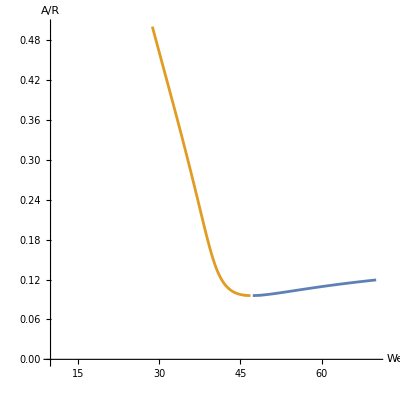

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"},PlotPoints->200]
```

```mathematica
n312ff=0.025 ((0.9914309834270436 c31^3-(4.4653203748882244*^-15-1.1536742597197513*^-16 ⅈ) d31+3.1713923117103876*^-17 c31^2 d31+1.1417012322157392*^-16 d31^3+c31 (-63.91139683345043+0.9914309834270438 d31^2)) Cos[t]+(-149.40824281595212 c31+7.930207165542526 c31^3+1.5856961558551938*^-17 c31^2 d31-23.790621496627573 c31 d31^2+7.928480779275969*^-18 d31^3) Cos[3. t]-1.6237528635957182*^-15 c31 Sin[t]+1.2685569246841548*^-16 c31^3 Sin[t]+(29.017679450995182-1.2690416856917258*^-15 ⅈ) d31 Sin[t]+0.9914309834270438 c31^2 d31 Sin[t]+5.0742276987366194*^-17 c31 d31^2 Sin[t]+0.9914309834270436 d31^3 Sin[t]-8.118764317978591*^-16 c31 Sin[3. t]+6.342784623420774*^-18 c31^3 Sin[3. t]-149.40824281595212 d31 Sin[3. t]+23.79062149662757 c31^2 d31 Sin[3. t]+9.51417693513116*^-18 c31 d31^2 Sin[3. t]-7.930207165542526 d31^3 Sin[3. t]);
```

```mathematica
k312ff=-0.2285228997322329 (d31 (35.97785333364035+0.6315205427364502 c31^2+0.6315205427364503 d31^2) Cos[t]+d31 (-19.11253279254025+2.7517777209898266 c31^2-0.9172592403299418 d31^2) Cos[3. t]+c31 (-54.09617018674671-0.6315205427364503 c31^2-0.6315205427364501 d31^2) Sin[t]+c31 (19.112532792540243-0.9172592403299418 c31^2+2.7517777209898258 d31^2) Sin[3. t]);
```

```mathematica
data
```

{0,0.768646,-32.6272,0,-0.326367,0,0.0822192,40,77/256}

```mathematica
dat
```

{0,-8.46633,-37.5432,0,-0.0910875,0,0.0822192,40,77/256}

```mathematica
2*(3+1)*n312ff(*-2*D[k312ff,t]*)//Chop//TrigReduce
```

-12.3652 c31 Cos[t]+0.215439 c31^3 Cos[t]+0.215439 c31 d31^2 Cos[t]-37.7848 c31 Cos[3. t]+1.66234 c31^3 Cos[3. t]-4.98703 c31 d31^2 Cos[3. t]+7.49938 d31 Sin[t]+0.215439 c31^2 d31 Sin[t]+0.215439 d31^3 Sin[t]-37.7848 d31 Sin[3. t]+4.98703 c31^2 d31 Sin[3. t]-1.66234 d31^3 Sin[3. t]

```mathematica
2*v31ff[0,0,3]*(3+1)(*-2*D[u311,t]*)(*-4*delta*(kr+1)(kr+2)*u311*)//TrigReduce
```

-2.91187 c0 Cos[t]+0.0101804 c0^3 Cos[t]+0.0101804 c0 d0^2 Cos[t]-36.1937 c0 Cos[3 t]+1.6382 c0^3 Cos[3 t]-4.91459 c0 d0^2 Cos[3 t]+15.6312 d0 Sin[t]+0.0101804 c0^2 d0 Sin[t]+0.0101804 d0^3 Sin[t]-36.1937 d0 Sin[3 t]+4.91459 c0^2 d0 Sin[3 t]-1.6382 d0^3 Sin[3 t]

```mathematica
v31ff[0,0,3]
```

-0.363984 c0 Cos[t]+0.00127255 c0^3 Cos[t]+0.00127255 c0 d0^2 Cos[t]-4.52422 c0 Cos[3 t]+0.204775 c0^3 Cos[3 t]-0.614324 c0 d0^2 Cos[3 t]+1.9539 d0 Sin[t]+0.00127255 c0^2 d0 Sin[t]+0.00127255 d0^3 Sin[t]-4.52422 d0 Sin[3 t]+0.614324 c0^2 d0 Sin[3 t]-0.204775 d0^3 Sin[3 t]

```mathematica
n312ff//Chop//Expand
```

-1.59778 c31 Cos[t]+0.0247858 c31^3 Cos[t]+0.0247858 c31 d31^2 Cos[t]-3.73521 c31 Cos[3. t]+0.198255 c31^3 Cos[3. t]-0.594766 c31 d31^2 Cos[3. t]+0.725442 d31 Sin[t]+0.0247858 c31^2 d31 Sin[t]+0.0247858 d31^3 Sin[t]-3.73521 d31 Sin[3. t]+0.594766 c31^2 d31 Sin[3. t]-0.198255 d31^3 Sin[3. t]

```mathematica
u311
```

-8.22176 d0 Cos[t]-0.144317 c0^2 d0 Cos[t]-0.144317 d0^3 Cos[t]+4.36765 d0 Cos[3 t]-0.628844 c0^2 d0 Cos[3 t]+0.209615 d0^3 Cos[3 t]+12.3622 c0 Sin[t]+0.144317 c0^3 Sin[t]+0.144317 c0 d0^2 Sin[t]-4.36765 c0 Sin[3 t]+0.209615 c0^3 Sin[3 t]-0.628844 c0 d0^2 Sin[3 t]

```mathematica
k312ff//Expand
```

-8.22176 d31 Cos[t]-0.144317 c31^2 d31 Cos[t]-0.144317 d31^3 Cos[t]+4.36765 d31 Cos[3. t]-0.628844 c31^2 d31 Cos[3. t]+0.209615 d31^3 Cos[3. t]+12.3622 c31 Sin[t]+0.144317 c31^3 Sin[t]+0.144317 c31 d31^2 Sin[t]-4.36765 c31 Sin[3. t]+0.209615 c31^3 Sin[3. t]-0.628844 c31 d31^2 Sin[3. t]

```mathematica
2*(Sin[t])*(kr+1)*(f31*b312sol)
```

77/128 (1+kr) Sin[t] (1.1041 d31-0.0375406 d31 Cos[2 t]+0.0750812 c31 Cos[t] Sin[t])

```mathematica
2*(bo/(ϵ*wer)+Sin[t])*(kr+1)*(f31*b311sol)
```

77/128 (1+kr) (bo/(40 ϵ)+Sin[t]) (1.1041 d0-0.0375406 d0 Cos[2 t]+0.0375406 c0 Sin[2 t])

```mathematica
b312sol
```

1.1041 d31-0.0375406 d31 Cos[2 t]+0.0750812 c31 Cos[t] Sin[t]

```mathematica
b311sol
```

1.1041 d0-0.0375406 d0 Cos[2 t]+0.0375406 c0 Sin[2 t]

```mathematica
forc313
```

-37.5432 c31 Cos[t]-0.0910875 c31^3 Cos[t]-0.0910875 c31 d31^2 Cos[t]-0.045166 c31 Cos[3 t]-4.90667 c31 Cos[3. t]+0.350977 c31^3 Cos[3. t]-1.05293 c31 d31^2 Cos[3. t]-8.46633 d31 Sin[t]-0.0910875 c31^2 d31 Sin[t]-0.0910875 d31^3 Sin[t]-0.045166 d31 Sin[3 t]-4.90667 d31 Sin[3. t]+1.05293 c31^2 d31 Sin[3. t]-0.350977 d31^3 Sin[3. t]

```mathematica
forcing
```

-32.6272 c0 Cos[t]-0.326367 c0^3 Cos[t]-0.326367 c0 d0^2 Cos[t]-11.2128 c0 Cos[3 t]+0.428423 c0^3 Cos[3 t]-1.28527 c0 d0^2 Cos[3 t]+0.768646 d0 Sin[t]-0.326367 c0^2 d0 Sin[t]-0.326367 d0^3 Sin[t]-11.2128 d0 Sin[3 t]+1.28527 c0^2 d0 Sin[3 t]-0.428423 d0^3 Sin[3 t]

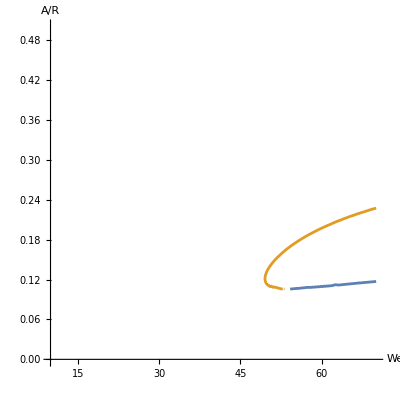

```mathematica
h31eqn[0.026,3]
```

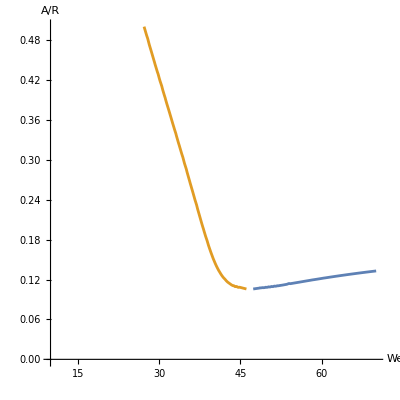

```mathematica
harmonic31fun[0.026,0,3]
```

```mathematica
data
```

{0,1.88955-6.87187 b051t^2,-27.5911-6.87187 b051t^2,0,-0.278453,0,0.0822192,40,77/256}

```mathematica
b312fun[0,3]
```

1.1041 d31-0.0375406 d31 Cos[2 t]+0.0750812 c31 Cos[t] Sin[t]

```mathematica
n312ff
```

1/40 (c31 (-61.8259+1.07719 c31^2+1.07719 d31^2) Cos[t]+c31 (-188.924+8.31171 c31^2-24.9351 d31^2) Cos[3. t]+d31 (37.4969+1.07719 c31^2+1.07719 d31^2) Sin[t]+d31 (-188.924+24.9351 c31^2-8.31171 d31^2) Sin[3. t])

```mathematica
v31ff[0,0,3]
```

-1.01423 c0 Cos[t]-0.00471663 c0^3 Cos[t]-0.00471663 c0 d0^2 Cos[t]-4.74125 c0 Cos[3 t]+0.210764 c0^3 Cos[3 t]-0.632292 c0 d0^2 Cos[3 t]+1.81734 d0 Sin[t]-0.00471663 c0^2 d0 Sin[t]-0.00471663 d0^3 Sin[t]-4.74125 d0 Sin[3 t]+0.632292 c0^2 d0 Sin[3 t]-0.210764 d0^3 Sin[3 t]

## notation: must read for validation

```mathematica
ϕ[r,θ,φ,t]=e*ϕ1[r,θ,φ,t]+e^2*ϕ2[r,θ,φ,t]+e^3*ϕ3[r,θ,φ,t];
η[θ,φ,t]=e* η1[θ,φ,t]+e^2* η2[θ,φ,t]+e^3* η3[θ,φ,t];
```

```mathematica
D[ϕ[r,θ,φ,t],r]/.r->1+η[θ,φ,t]
```

e ϕ1^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^2 ϕ2^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^3 ϕ3^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]

```mathematica
Series[D[ϕ[r,θ,φ,t],r]/.r->1+η[θ,φ,t],{e,0,3}]
```

ϕ1^(1,0,0,0)[1,θ,φ,t] e+(ϕ2^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]) e^2+(ϕ3^(1,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ1^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ2^(2,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ1^(3,0,0,0)[1,θ,φ,t]) e^3+O[e]^4

```mathematica
normalstr1e1
```

-Cos[t] Cos[θ]+1/We 2 (1/8 √(5/π) b201[t] (1+3 Cos[2 θ])+(3 b401[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(128 √π)-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ])-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] Sin[θ] a311'[t]+(3 (9+20 Cos[2 θ]+35 Cos[4 θ]) a401'[t])/(128 √π)-1/24 √(5/π) (1+3 Cos[2 θ]) b201''[t]

```mathematica
(2 η1[θ,φ,t]-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])/We
```

1/We 2 (1/8 √(5/π) b201[t] (1+3 Cos[2 θ])+(3 b401[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(128 √π)-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ])

```mathematica
Integrate[(1/We(2 η1[θ,φ,t]-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

b201[t]/We

```mathematica
Integrate[(2 η1[θ,φ,t]-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])/We*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

b311[t]/We

```mathematica
η1[θ,φ,t]
```

1/8 √(5/π) b201[t] (1+3 Cos[2 θ])+(3 b401[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(128 √π)-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]

```mathematica
Derivative[0,2,0][η1][θ,φ,t]/.η1->Function[{θ,φ,t},1/8 √(5/π) b201[t] (1+3 Cos[2 θ])+(3 b401[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(128 √π)-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]]
```

0

```mathematica
Integrate[((*2 η1[θ,φ,t]*)-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

0

```mathematica
Derivative[0,2,0][η1][θ,φ,t]
```

```mathematica
ruleDerToD=HoldPattern[(Derivative[ords__][f_])[args__]]:>Module[{o={ords},a={args}},D[f@@a,Sequence@@MapThread[List,{a,o}]]];
```

```mathematica
tryrule=Derivative[0,2,0][η1][θ,φ,t]/.ruleDerToD
```

0

```mathematica
normalstr1e1
```

-Cos[t] Cos[θ]+1/We 2 (1/8 √(5/π) b201[t] (1+3 Cos[2 θ])+(3 b401[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(128 √π)-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ])+1/8 √(5/π) (1+3 Cos[2 θ]) a201'[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] Sin[θ] a311'[t]+(3 (9+20 Cos[2 θ]+35 Cos[4 θ]) a401'[t])/(128 √π)

```mathematica
-Cos[t] Cos[θ]+1/We((*2 η1[θ,φ,t]*)-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])(*+ϕ1^(0,0,0,1)[1,θ,φ,t]*)
```

-Cos[t] Cos[θ]+1/We(3/2 √(5/π) b201[t] Cos[2 θ]-(3 b401[t] (-80 Cos[2 θ]-560 Cos[4 θ]))/(128 √π)-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Csc[θ]-5/2 √(21/(2 π)) b311[t] Cos[2 θ] Cos[φ] Sin[θ]-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]-5/2 √(21/(2 π)) b311[t] Cos[θ] Cos[φ] Sin[2 θ]-Cot[θ] (-1/8 √(21/(2 π)) b311[t] Cos[θ] (3+5 Cos[2 θ]) Cos[φ]-3/4 √(5/π) b201[t] Sin[2 θ]+5/4 √(21/(2 π)) b311[t] Cos[φ] Sin[θ] Sin[2 θ]+(3 b401[t] (-40 Sin[2 θ]-140 Sin[4 θ]))/(128 √π)))

```mathematica
Derivative[1,0,0][η1][θ,φ,t]
```

-3/4 √(5/π) b201[t] Sin[2 θ]

```mathematica
crt[o_,p_]:=Symbol["a"<>ToString[o]<>ToString[p]<>ToString[1]][t]
```

```mathematica
crt[2,0]
```

a201[t]

```mathematica
Clear[a201,a311,a401]
kinproj=Integrate[kinematicr1e1*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
rule=First@Solve[kinproj==0,a201[t]];
a201[x_]:=Evaluate[(a201[t]/.rule)/.t->x];
eqn=Integrate[normalstr1e1*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
Clear[a201];
exps=b201[t]/.Flatten[DSolve[eqn==0,b201[t],t]]/.{C[1]->0,C[2]->0};
a201[y_]:=(exps/.t->y
)
```

```mathematica
a201[t]
```

(3 √(5 π) We Sin[t])/(4 (-12+We))

```mathematica
kinproj
```

```mathematica
Clear[a311,a401]
kinproj=Integrate[kinematicr1e1*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
rule=First@Solve[kinproj==0,a311[t]];
a311[x_]:=Evaluate[(a311[t]/.rule)/.t->x];
eqn=Integrate[normalstr1e1*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
Clear[a311];
exps=b311[t]/.Flatten[DSolve[eqn==0,b311[t],t]]/.{C[1]->c31,C[2]->d31};
a311[y_]:=(exps/.t->y
)
```

```mathematica
Clear[a401]
kinproj=Integrate[kinematicr1e1*realkl[4,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
rule=First@Solve[kinproj==0,a401[t]];
a401[x_]:=Evaluate[(a401[t]/.rule)/.t->x];
eqn=Integrate[normalstr1e1*realkl[4,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
Clear[a401];
exps=b401[t]/.Flatten[DSolve[eqn==0,b401[t],t]]/.{C[1]->0,C[2]->0};
a401[y_]:=(exps/.t->y
)
```

```mathematica
a401[t]
```

-(5 √π We Sin[t])/(8 (-90+We))

```mathematica
ampe1[40]
```

```mathematica
b311[y]
```

c31 Cos[y]+d31 Sin[y]

```mathematica
eqn202
```

0

```mathematica
Clear[a202,b202,a312,a402]
```

```mathematica
Clear[a201,b201,a311,b311,a401,b401,a202,b202,a312,a402]
kinproj202=Integrate[kinematicr1e2*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
rule202=First@Solve[kinproj202==0,a202[t]];
a202[x_]:=Evaluate[(a202[t]/.rule202)/.t->x];
eqn202=Integrate[normalstr1e2*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ampe1[40];
exps202=b202[t]/.Flatten[DSolve[TrigReduce[eqn202]==0,b202[t],t]/.{C[1]->0,C[2]->0,We->40}]//FullSimplify;
b202[y_]:=(exps202/.{t->y})
```

```mathematica
kinematicr1e2
```

3/8 √(5/π) a202[t] (1+3 Cos[2 θ])+(15 a402[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(128 √π)-1/2 √(21/(2 π)) a312[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]-(3/2 √(5/π) a201[t] (1+3 Cos[2 θ])+(45 a401[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(64 √π)-5/2 √(21/(2 π)) a311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]) (1/8 √(5/π) b201[t] (1+3 Cos[2 θ])+(3 b401[t] (9+20 Cos[2 θ]+35 Cos[4 θ]))/(128 √π)-1/8 √(21/(2 π)) b311[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ])+(-1/8 √(21/(2 π)) a311[t] Cos[θ] (3+5 Cos[2 θ]) Cos[φ]-3/4 √(5/π) a201[t] Sin[2 θ]+5/4 √(21/(2 π)) a311[t] Cos[φ] Sin[θ] Sin[2 θ]+(3 a401[t] (-40 Sin[2 θ]-140 Sin[4 θ]))/(128 √π)) (-1/8 √(21/(2 π)) b311[t] Cos[θ] (3+5 Cos[2 θ]) Cos[φ]-3/4 √(5/π) b201[t] Sin[2 θ]+5/4 √(21/(2 π)) b311[t] Cos[φ] Sin[θ] Sin[2 θ]+(3 b401[t] (-40 Sin[2 θ]-140 Sin[4 θ]))/(128 √π))+(21 a311[t] b311[t] (3+5 Cos[2 θ])^2 Sin[φ]^2)/(128 π)+1/8 √(5/π) (1+3 Cos[2 θ]) b202'[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] Sin[θ] b312'[t]+(3 (9+20 Cos[2 θ]+35 Cos[4 θ]) b402'[t])/(128 √π)

```mathematica
kinproj202=Integrate[kinematicr1e2*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

1/(308 √(5 π))(-847 a311[t] b311[t]-20 a401[t] (66 √5 b201[t]+65 b401[t])-66 a201[t] (15 b201[t]+2 √5 b401[t])+154 √(5 π) (3 a202[t]+b202'[t]))

```mathematica
eqn202=Integrate[normalstr1e2*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

1/(19712 √(5 π) We)(61600 We a311[t]^2-385 √π We (16 √5 b201[t]+13 b401[t]) Sin[t]+64 (1870 b201[t]^2-616 √(5 π) b202[t]+2695 b311[t]^2+5016 √5 b201[t] b401[t]+5900 b401[t]^2+2 We (330 a201[t]^2+825 √5 a201[t] a401[t]+1050 a401[t]^2-33 (5 b201[t]+3 √5 b401[t]) a201'[t]+77 (√(5 π) a202'[t]-2 b311[t] a311'[t])-5 (33 √5 b201[t]+50 b401[t]) a401'[t])))

```mathematica
kinproj312=Integrate[kinematicr1e2*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

2 a312[t]+1/(220 √π)(-99 √5 a201[t] b311[t]-100 a401[t] b311[t]-a311[t] (187 √5 b201[t]+50 b401[t])+110 √π b312'[t])

```mathematica
kinproj402=Integrate[kinematicr1e2*realkl[4,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

1/(2002 √π)(-78 (88 a201[t]+45 √5 a401[t]) b201[t]-819 a311[t] b311[t]-90 (13 √5 a201[t]+54 a401[t]) b401[t]+1001 √π (5 a402[t]+b402'[t]))

```mathematica
eqn312=Integrate[normalstr1e2*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

3/4 √(5/π) a201[t] a311[t]+(15 a311[t] a401[t])/(22 √π)-77/512 ⅈ ⅇ^(-ⅈ t) b311[t]+77/512 ⅈ ⅇ^(ⅈ t) b311[t]+(13 b201[t] b311[t])/(√(5 π) We)-(5 b312[t])/We+(47 b311[t] b401[t])/(22 √π We)-(3 b311[t] a201'[t])/(4 √(5 π))-(b201[t] a311'[t])/(√(5 π))-(b401[t] a311'[t])/(11 √π)+a312'[t]/2-(5 b311[t] a401'[t])/(44 √π)

```mathematica
eqn402=Integrate[normalstr1e2*realkl[4,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

1/(256256 √π We)(137280 We a201[t]^2+52416 We a311[t]^2+299520 √5 We a201[t] a401[t]+544320 We a401[t]^2+933504 b201[t]^2+203840 b311[t]^2+1264640 √5 b201[t] b401[t]+1835136 b401[t]^2-2306304 √π b402[t]-13013 √(5 π) We b201[t] Sin[t]-81081 √π We b401[t] Sin[t]-164736 We b201[t] a201'[t]-49920 √5 We b401[t] a201'[t]-23296 We b311[t] a311'[t]-83200 √5 We b201[t] a401'[t]-155520 We b401[t] a401'[t]+128128 √π We a402'[t])

```mathematica
rule202
```

{a202[t]→1/(2310 √π)(990 √5 a201[t] b201[t]+6600 a401[t] b201[t]+847 √5 a311[t] b311[t]+660 a201[t] b401[t]+1300 √5 a401[t] b401[t]-770 √π b202'[t])}

```mathematica
a202[x]
```

1/(2310 √π)(990 √5 a201[x] b201[x]+6600 a401[x] b201[x]+847 √5 a311[x] b311[x]+660 a201[x] b401[x]+1300 √5 a401[x] b401[x]-770 √π b202'[x])

```mathematica
b201[y]
```

15/14 √(5 π) Sin[y]

```mathematica
eqn202
```

1/(19712 √(5 π) We)(-71005/2 π We Sin[t]^2+3850 We (-d31 Cos[t]+c31 Sin[t])^2+64 (-616 √(5 π) b202[t]+2513125/98 π Sin[t]^2+2695 (c31 Cos[t]+d31 Sin[t])^2+2 We (72183/196 π Cos[t]^2-98975/196 π Sin[t]^2+77 (-1/2 (c31 Cos[t]+d31 Sin[t])^2+1/(462 √5)(-272845/98 √5 π Cos[t]^2+272845/98 √5 π Sin[t]^2+847/4 √5 (d31 Cos[t]-c31 Sin[t]) (-d31 Cos[t]+c31 Sin[t])+847/4 √5 (c31 Cos[t]+d31 Sin[t])^2-770 √π b202''[t])))))

```mathematica
b202[y]
```

1/35737856(√(5 π) (-43398521+3687089 Cos[2 y])-15092 √(5/π) (-777 (c31^2+d31^2)+89 (c31-d31) (c31+d31) Cos[2 y]+178 c31 d31 Sin[2 y]))

```mathematica
b312[y]//N//Expand
```

-0.529748 d31+0.228991 d31 Cos[2. y]-0.228991 c31 Sin[2. y]

```mathematica
exps202=b202[t]/.Flatten[DSolve[TrigReduce[eqn202]==0,b202[t],t]/.{C[1]->0,C[2]->0,We->40}]//FullSimplify;
b202[y_]:=(exps202/.{t->y});
```

```mathematica
b201[w]//N
```

4.24642 Sin[w]

```mathematica
eqn202//TrigReduce
```

1/(57953280 √π We)(50709120 √5 c31^2+50709120 √5 d31^2+482520000 √5 π-316932 √5 c31^2 We-316932 √5 d31^2 We-15581799 √5 π We-115906560 √π b202[t]+50709120 √5 c31^2 Cos[2 t]-50709120 √5 d31^2 Cos[2 t]-482520000 √5 π Cos[2 t]+75460 √5 c31^2 We Cos[2 t]-75460 √5 d31^2 We Cos[2 t]+8375911 √5 π We Cos[2 t]+101418240 √5 c31 d31 Sin[2 t]+150920 √5 c31 d31 We Sin[2 t]-9658880 √π We b202''[t])

```mathematica
b202[t]/.Flatten[DSolve[TrigReduce[eqn202]==0,b202[t],t]/.{C[1]->0,C[2]->0,We->40}]//FullSimplify
```

1/35737856(√(5 π) (-43398521+3687089 Cos[2 t])-15092 √(5/π) (-777 (c31^2+d31^2)+89 (c31-d31) (c31+d31) Cos[2 t]+178 c31 d31 Sin[2 t]))

```mathematica
Clear[a202,b202,a312,a402]
kinproj202=Integrate[kinematicr1e2*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
rule202=First@Solve[kinproj202==0,a202[t]];
a202[x_]:=Evaluate[(a202[t]/.rule202)/.t->x];
eqn202=Integrate[normalstr1e2*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
Clear[b202];
ampe1[40];
exps202=b202[t]/.Flatten[DSolve[{eqn202/.We->40}==0,b202[t],t]]/.{C[1]->0,C[2]->0};
b202[y_]:=(exps202/.{t->y});
```

Solve::ivar: -1/10 √π Cos[t] is not a valid variable.

ReplaceAll::reps: {(3 a202[t])/2+(83006 c31 d31 Cos[Times[«2»]]+(Times[«3»]+Times[«2»]) Sin[Times[«2»]])/(120736 √(5 π))+b202'[t]/2==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(3 a202[x])/2+(83006 c31 d31 Cos[Times[«2»]]+(Times[«3»]+Times[«2»]) Sin[Times[«2»]])/(120736 √(5 π))+b202'[x]/2==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::deqx: Supplied equations are not differential or integral equations of the given functions.

ReplaceAll::reps: {DSolve[{0}==0,b202[t],t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
kinproj202=1/(308 √(5 π))(-847 a311[t] b311[t]-20 a401[t] (66 √5 b201[t]+65 b401[t])-66 a201[t] (15 b201[t]+2 √5 b401[t])+154 √(5 π) (3 a202[t]+b202'[t]));
```

```mathematica
kinproj202//N//Expand
```

1.5 a202[t]-0.811007 a201[t] b201[t]-2.41796 a401[t] b201[t]-0.693861 a311[t] b311[t]-0.241796 a201[t] b401[t]-1.06496 a401[t] b401[t]+0.5 b202'[t]

```mathematica
rule202=First@Solve[kinproj202==0,a202[t]]
```

{a202[t]→1/(2310 √π)(990 √5 a201[t] b201[t]+6600 a401[t] b201[t]+847 √5 a311[t] b311[t]+660 a201[t] b401[t]+1300 √5 a401[t] b401[t]-770 √π b202'[t])}

```mathematica
a202[x_]:=Evaluate[(a202[t]/.rule202)/.t->x]
```

```mathematica
eqn=Integrate[normalstr1e2*realkl[2,0]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

1/8 √(5/π) ((24 a201[t]^2)/7+5 a311[t]^2+(120 a401[t]^2)/11+(68 b201[t]^2)/(7 We)-(16 √(π/5) b202[t])/We+(14 b311[t]^2)/We+(912 b201[t] b401[t])/(7 √5 We)+(2360 b401[t]^2)/(77 We)-1/2 √(5 π) b201[t] Sin[t]-13/32 √π b401[t] Sin[t]-(4 b401[t] a201'[t])/(√5)-2/15 b311[t] a311'[t]+4/7 √5 b201[t] a401'[t]-80/231 b401[t] a401'[t]+16/7 √5 a401[t] b201'[t]+22/15 a311[t] b311'[t]+520/231 a401[t] b401'[t]+4/35 a201[t] (75 √5 a401[t]+15 b201'[t]+2 √5 b401'[t])-4/3 √(π/5) b202''[t])

```mathematica
sls=eqn202/.We->40//TrigReduce
```

1/(57953280 √π)(950796 √5 c31^2+950796 √5 d31^2-3518799 √5 π-2897664 √π b202[t]+1343188 √5 c31^2 Cos[2 t]-1343188 √5 d31^2 Cos[2 t]-3687089 √5 π Cos[2 t]+2686376 √5 c31 d31 Sin[2 t]-9658880 √π b202''[t])

```mathematica
exps202=b202[t]/.Flatten[DSolve[sls==0,b202[t],t]]/.{C[1]->0,C[2]->0}
```

1/(35737856 √π)(11726484 √5 c31^2 Cos[√(3/10) t]^2+11726484 √5 d31^2 Cos[√(3/10) t]^2-43398521 √5 π Cos[√(3/10) t]^2-1343188 √5 c31^2 Cos[2 t] Cos[√(3/10) t]^2+1343188 √5 d31^2 Cos[2 t] Cos[√(3/10) t]^2+3687089 √5 π Cos[2 t] Cos[√(3/10) t]^2-2686376 √5 c31 d31 Cos[√(3/10) t]^2 Sin[2 t]+11726484 √5 c31^2 Sin[√(3/10) t]^2+11726484 √5 d31^2 Sin[√(3/10) t]^2-43398521 √5 π Sin[√(3/10) t]^2-1343188 √5 c31^2 Cos[2 t] Sin[√(3/10) t]^2+1343188 √5 d31^2 Cos[2 t] Sin[√(3/10) t]^2+3687089 √5 π Cos[2 t] Sin[√(3/10) t]^2-2686376 √5 c31 d31 Sin[2 t] Sin[√(3/10) t]^2)

```mathematica
FullSimplify[exps202]
```

1/35737856(√(5 π) (-43398521+3687089 Cos[2 t])-15092 √(5/π) (-777 (c31^2+d31^2)+89 (c31-d31) (c31+d31) Cos[2 t]+178 c31 d31 Sin[2 t]))

```mathematica
Coefficient[1/35737856(√(5 π) (-43398521+3687089 Cos[2 t])-15092 √(5/π) (-777 (c31^2+d31^2)+89 (c31-d31) (c31+d31) Cos[2 t]+178 c31 d31 Sin[2 t])),Cos[2t]]//N//Expand
```

0.408898-0.0474153 c31^2+0.0474153 d31^2

```mathematica
Expand[1.2698150247948368*^-9 (-1.8212647068731883*^8+8.841645334103828*^6 c31^2-8.841645334103828*^6 d31^2)]
```

-0.231267+0.0112273 c31^2-0.0112273 d31^2

```mathematica
aaa=exps202//TrigReduce//Simplify//Chop
```

1/(44430848 √(5 π))(92 (328251 c31^2+328251 d31^2+4082710 π)-4 (-494263 c31^2+494263 d31^2+3240770 π) Cos[2 t]+539 (7336 c31 d31+96825 π) Sin[2 t])

```mathematica
Coefficient[aaa,Cos[2t]]//Expand//N
```

-0.231267+0.0112273 c31^2-0.0112273 d31^2

```mathematica
kinproj=Integrate[kinematicr1e1*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
```

```mathematica
kinproj
```

1/2 (4 a311[t]+b311'[t])

```mathematica
rule=First@Solve[kinproj==0,a311[t]]
```

{a311[t]→-1/4 b311'[t]}

```mathematica
a311[x_]:=Evaluate[(a311[t]/.rule)/.t->x]
```

```mathematica
eqn=Integrate[normalstr1e1*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

-(5 b311[t])/We-b311''[t]/8

```mathematica
exps=b311[t]/.Flatten[DSolve[eqn==0,b311[t],t]]
```

C[1] Cos[(2 √10 t)/(√We)]+C[2] Sin[(2 √10 t)/(√We)]

```mathematica
b311[y_]:=(exps/.t->y)
```

```mathematica
b311[s]
```

c31 Cos[(2 √10 s)/(√We)]+d31 Sin[(2 √10 s)/(√We)]

```mathematica
b311[s]
```

c31 Cos[(2 √10 s)/(√We)]+d31 Sin[(2 √10 s)/(√We)]

```mathematica
a311[s]
```

1/4 (-(2 √10 d31 Cos[(2 √10 s)/(√We)])/(√We)+(2 √10 c31 Sin[(2 √10 s)/(√We)])/(√We))

```mathematica
b401[s]
```

-(5 √π We Sin[s])/(8 (-90+We))

```mathematica
b201[s]
```

(3 √(5 π) We Sin[s])/(4 (-12+We))

```mathematica
exps
```

(3 √(5 π) We Sin[t])/(4 (-12+We))

```mathematica
(*kinproj=Integrate[kinematicr1e1*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
rule=First@Solve[kinproj==0,a311[t]];*)
a311[x_]:=Evaluate[(a311[t]/.rule)/.t->x];
eqn=Integrate[normalstr1e1*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
Clear[b311];
exps=b311[t]/.Flatten[DSolve[eqn==0,b311[t],t]]/.{C[1]->c31,C[2]->d31};
b311[y_]:=(exps/.t->y)
```

```mathematica
a311[c]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

TerminatedEvaluation[IterationLimit]

```mathematica
b3
```

```mathematica
Clear[a311]
```

```mathematica
harmonic31fff[oh_,bo_,kr_]:=(Clear[c0,d0,b311sol,we,wer,f31,zetak,delta];
k=kr;

wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
zetak=wer/we;
f31=Integrate[Cos[θ]*realkl[3,1]*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
b311sol=b311fun[0,bo,kr];
u311=u31ff[0,bo,kr];
forcing=2*(bo/(ϵ*wer)+Sin[t])*(kr+1)*(f31*b311sol)+2*v31ff[0,bo,kr]*(kr+1)-2*D[u311,t](*-4*delta*(kr+1)(kr+2)*u311*)//TrigReduce;
fcos=Integrate[(1/Pi)*forcing*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forcing*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c0]-Coefficient[fsin,c0*d0^2]*d0^2//FullSimplify//Chop;g2=Coefficient[fsin,d0]-Coefficient[fsin,d0*c0^2]*c0^2//FullSimplify//Chop;g3=Coefficient[fcos,c0]-Coefficient[fcos,c0*d0^2]*d0^2//FullSimplify//Chop;g4=Coefficient[fcos,d0]-Coefficient[fcos,d0*c0^2]*c0^2//FullSimplify//Chop;
α=Coefficient[fcos,c0^3]//Chop;
β=Coefficient[fcos,d0^3]//Chop;

wer=(kr^2-1)(kr+2);
delta=oh/(√wer);dkr=delta*(kr+1)*(kr+2);
Δk=dkr;
data={g1,g2,g3,g4,α,β,dkr,wer,f31};ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
)
```

```mathematica
eta1
```

1/4 √(5/π) b201ff[t] (-1+3 Cos[θ]^2)+(3 b401ff[t] (3-30 Cos[θ]^2+35 Cos[θ]^4))/(16 √π)-1/8 √(21/(2 π)) b311ff[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]

```mathematica
eta1=b201ff[c]*realklpt[2,0,θ,φ]+b311ff[c]*realklpt[3,1,θ,φ]+b401ff[c]*realklpt[4,0,θ,φ]/.c->t;
```

```mathematica
eta1
```

1/4 √(5/π) b201ff[t] (-1+3 Cos[θ]^2)+(3 b401ff[t] (3-30 Cos[θ]^2+35 Cos[θ]^4))/(16 √π)-1/8 √(21/(2 π)) b311ff[t] (3+5 Cos[2 θ]) Cos[φ] Sin[θ]

```mathematica
Clear[phi1]
```

```mathematica
phi1=-D[b201ff[c],c]/(3 r^3)*realklpt[2,0,θ,φ]-D[b311ff[c],c]/(4 r^4)*realklpt[3,1,θ,φ]-D[b401ff[c],c]/(5 r^5)*realklpt[4,0,θ,φ]/.c->t;
```

```mathematica
phi0=-D[b201ff[c],c]/(3 r^3)*realklpt[2,0,θ,φ]/.c->t;
```

```mathematica
phi11=-D[b201ff[c],c]/(3 r^3)*realklpt[2,0,θ,φ]/.c->t;
```

```mathematica
eta2=b202ff[c]*realklpt[2,0,θ,φ]+b312ff[c]*realklpt[3,1,θ,φ]+b402ff[c]*realklpt[4,0,θ,φ]/.c->t;
```

```mathematica
phi2=-(D[b202ff[c],c]+2k201fff[c])/(3 r^3)*realklpt[2,0,θ,φ]-(D[b312ff[c],c]+2k311fff[c])/(4 r^4)*realklpt[3,1,θ,φ]-(D[b402ff[c],c]+2k401fff[c])/(5 r^5)*realklpt[4,0,θ,φ]/.c->t;
```

```mathematica
phi1t=D[phi1,t];
```

```mathematica
phi2t=D[phi2,t];
```

```mathematica
D[eta1,t]
```

1/4 √(5/π) (-1+3 Cos[θ]^2) b201ff'[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] Sin[θ] b311ff'[t]+(3 (3-30 Cos[θ]^2+35 Cos[θ]^4) b401ff'[t])/(16 √π)

```mathematica
phi2t
```

-(√(5/π) (-1+3 Cos[θ]^2) (2 k201fff'[t]+b202ff''[t]))/(12 r^3)+(√(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] Sin[θ] (2 k311fff'[t]+b312ff''[t]))/(32 r^4)-(3 (3-30 Cos[θ]^2+35 Cos[θ]^4) (2 k401fff'[t]+b402ff''[t]))/(80 √π r^5)

```mathematica
realkl[3,1]-realklpt[3,1,θ,φ]
```

0

```mathematica
v31term=eta1^2/2*D[phi1t,r,r]+eta1*D[phi2t,r]+eta2*D[phi1t,r]+D[phi1,r]*D[phi2,r]+D[phi1,θ]*D[phi2,θ]+1/Sin[θ]^2*D[phi1,φ]*D[phi2,φ]+eta1*D[phi1,r]*D[phi1,r,r]+eta1*D[phi1,θ]*D[phi1,r,θ]+1/Sin[θ]^2*eta1*D[phi1,φ]*D[phi1,r,φ]-eta1*(D[phi1,θ]^2+1/Sin[θ]^2*D[phi1,φ]^2)-2/wer*(eta1*((1-2-2^2)*b202ff[t]*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b312ff[t]*realkl[3,1]+(1-4-4^2)*b402ff[t]*SphericalHarmonicY[4,0,θ,φ])+eta2*((1-2-2^2)*b201ff[t]*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b311ff[t]*realkl[3,1]+(1-4-4^2)*b401ff[t]*SphericalHarmonicY[4,0,θ,φ]));
```

```mathematica
v31=Integrate[TrigReduce[v31term]*realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Expand
```

```mathematica
b212fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));(*Print[ζk];*)
nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);hk=2*delta*μ2*(k+2);
k211ff=1.062854199665162 c21-3.977300088905001 d21+(-0.8833497767591527 c21-3.9819736147728015 d21) Cos[2. t]+(3.981973614772807 c21-0.8833497767591527 d21) Sin[2. t];
n211ff=1/We(c21 (-160.1988902869943+2.0024861285874254 We ρ1-6.007458385762286 We ρ2)+c21 (-160.1988902869943+30.03729192881145 We ρ1-26.032319671636593 We ρ2) Cos[2. t]+d21 (-160.1988902869943+30.03729192881145 We ρ1-26.032319671636593 We ρ2) Sin[2. t]);;
l211ff=-8.009944514349712 d21-88.10938965784686 d21 Cos[2. t]+88.10938965784686 c21 Sin[2. t];
ff21=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*realklpt[2,1,θ,φ],{θ,0,Pi/2},{φ,0,2Pi}];(*
ff30=Integrate[(SphericalHarmonicY[3,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)
f201=TrigReduce[nk*(b211[t]*Sin[t]*ff21)-D[k211ff,t]-2*delta*(k+1)(k+2)*k211ff+fk*n211ff-gk*D[l211ff,t]-hk*l211ff];
f1=Integrate[(1/(2Pi))*f201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((1/wem)(k^2-1)(k+2));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
k212ff//Chop//ExpToTrig//Simplify//Chop
```

(0.000545999 c21^3+c21^2 (0.0000684453-0.00655716 d21)+d21 (745.611+0.0000684453 d21-0.00655716 d21^2)+c21 (58.6525+0.000545999 d21^2)) Cos[t]+(-24.1142 c21-0.0000684453 c21^2+(0.10079-0.0000684453 d21) d21) Cos[1. t]+98.7372 c21 Cos[3. t]+0.001638 c21^3 Cos[3. t]-1945.65 d21 Cos[3. t]-0.0938822 c21^2 d21 Cos[3. t]-0.00491399 c21 d21^2 Cos[3. t]+0.0312941 d21^3 Cos[3. t]+408.423 c21 Sin[t]-0.0026289 c21^2 Sin[t]+0.00655716 c21^3 Sin[t]-17.1094 d21 Sin[t]+0.000545999 c21^2 d21 Sin[t]-0.0026289 d21^2 Sin[t]+0.00655716 c21 d21^2 Sin[t]+0.000545999 d21^3 Sin[t]-274.879 c21 Sin[1. t]+0.0026289 c21^2 Sin[1. t]+6.96288 d21 Sin[1. t]+0.0026289 d21^2 Sin[1. t]+1945.65 c21 Sin[3. t]+0.0312941 c21^3 Sin[3. t]+98.7372 d21 Sin[3. t]+0.00491399 c21^2 d21 Sin[3. t]-0.0938822 c21 d21^2 Sin[3. t]-0.001638 d21^3 Sin[3. t]

```mathematica
l212ff//Chop//ExpToTrig//Simplify//Chop
```

2.00249 d21+(-0.00436799 c21^3+c21^2 (-0.00254225+0.676422 d21)+c21 (-427.002-0.00436799 d21^2)+d21 (3874.11-0.00254225 d21+0.676422 d21^2)) Cos[t]+(148.492 c21+c21^2 (0.00254225-0.0487209 d21)+d21 (-186.796+0.00254225 d21-0.0487209 d21^2)) Cos[1. t]-38.0472 d21 Cos[2. t]-1055.21 c21 Cos[3. t]-0.017472 c21^3 Cos[3. t]+30928.9 d21 Cos[3. t]+2.77363 c21^2 d21 Cos[3. t]+0.0524159 c21 d21^2 Cos[3. t]-0.924544 d21^3 Cos[3. t]-13105.2 c21 Sin[t]+0.0976449 c21^2 Sin[t]-0.676422 c21^3 Sin[t]-9.37624 d21 Sin[t]-0.00436799 c21^2 d21 Sin[t]+0.0976449 d21^2 Sin[t]-0.676422 c21 d21^2 Sin[t]-0.00436799 d21^3 Sin[t]+3076.19 c21 Sin[1. t]-0.0976449 c21^2 Sin[1. t]+0.0487209 c21^3 Sin[1. t]+43.9682 d21 Sin[1. t]-0.0976449 d21^2 Sin[1. t]+0.0487209 c21 d21^2 Sin[1. t]+38.0472 c21 Sin[2. t]-30928.9 c21 Sin[3. t]-0.924544 c21^3 Sin[3. t]-1055.21 d21 Sin[3. t]-0.0524159 c21^2 d21 Sin[3. t]+2.77363 c21 d21^2 Sin[3. t]+0.017472 d21^3 Sin[3. t]

```mathematica
h21eqn[0.02,0.7,0.3,0.5,0.5,2,1]
```

-Graphics-

```mathematica
dat
```

{356.845,21895.,8040.72,237.092,-0.0127734,-0.00960255,0.0804984,wer,f31}